## BigSur Package

### External Packages to load

BoolEval is code from Szabolcs Horvát and is available at https : // github . com/szhorvat/BoolEval

```mathematica
<<BoolEval`
```

IGraphM is a paclet from Szabolcs Horvát, available at http://szhorvat.net/ which extends the functionality of IGraph to Mathematica

```mathematica
<<IGraphM`
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

### Manipulation of lists and matrices (Width, Unpack, SymmetricMatrixToList, SymmetricMatrixToListNew, ListToSymmetricMatrix, ListIndex, MatrixIndexCF, CutDown, DotProduct, DotProductCF)

#### Width

```mathematica
Width[mat_]:= Last[Dimensions[mat]]
```

#### Unpack

This takes a matrix and detects whether there are labels, i.e. non-numeric first rows or columns.  It then returns a list with three elements:  The matrix minus any labels, the row labels, and the column labels.  If no labels are present, it has {} in those positions.

```mathematica
Options[Unpack]={"Metadata"-> "No data", "Sparse"-> False};Unpack[mat_, opt:OptionsPattern[]]:= 

If[OptionValue["Sparse"]==True,
Which[NumberQ[mat[[1,2]]]&&NumberQ[mat[[2,1]]], {SparseArray[mat], {}, {},"Metadata"->  {OptionValue["Metadata"]}},
NumberQ[mat[[1,2]]]==False&&NumberQ[mat[[2,1]]], {SparseArray[Drop[mat,1]],{}, mat[[1]], "Metadata"->  {OptionValue["Metadata"]}},
NumberQ[mat[[1,2]]]&&NumberQ[mat[[2,1]]]==False, {SparseArray[mat[[All, 2;;]]],mat[[All,1]],{}, "Metadata"->  {OptionValue["Metadata"]}},
True, {SparseArray[mat[[2;;,2;;]]],mat[[2;;,1]],mat[[1,2;;]],"Metadata"->   {OptionValue["Metadata"]} }],
Which[NumberQ[mat[[1,2]]]&&NumberQ[mat[[2,1]]], {mat, {}, {},"Metadata"->  {OptionValue["Metadata"]}},
NumberQ[mat[[1,2]]]==False&&NumberQ[mat[[2,1]]], {Drop[mat,1],{}, mat[[1]], "Metadata"->  {OptionValue["Metadata"]}},
NumberQ[mat[[1,2]]]&&NumberQ[mat[[2,1]]]==False, {mat[[All, 2;;]],mat[[All,1]],{}, "Metadata"->  {OptionValue["Metadata"]}},
True, {mat[[2;;,2;;]],mat[[2;;,1]],mat[[1,2;;]],"Metadata"->   {OptionValue["Metadata"]} }]
]
```

We will call the list format produced by this function a “matpac” format.

This creates triples by adding each of the elements of list to the end of {x,y}.

```mathematica
AddThird[{x_,y_},list_]:= {x,y,#}&/@list
```

#### SymmetricMatrixToList

There are times when it is inconvenient to store a symmetric matrix as a matrix, and easier to store it as a flat list, especially when combining matrices, and when the have been lower-triangularized.  The following code replaces a symmetric matrix with the values of the Array Rules that would result from the Lower-triangularized version of the matrix.  Note that there should be Binomial[m,2] values, where m- is the common dimension or the original matrix

```mathematica
SymmetricMatrixToList[matrix_]:=Values[Drop[ArrayRules[SparseArray[LowerTriangularize[matrix, -1]]],-1]]
```

Interestingly, this runs rather slowly for big matrices.  A faster code would be to just use ExplicitValues, but that assumes there are no default values within the lower-triangularized portion of the matrix; if there were it would skip them

```mathematica
SymmetricMatrixToListAlt[matrix_]:=SparseArray[LowerTriangularize[matrix, -1]]["ExplicitValues"]
```

Actually it seems both codes will do that.  We need to check whether SymmetricMatrixToList is ever used on a matrix with zeros in the lower triangularized part.  Empirically it looks like that never happens, but we might want to insert some kind of a check, like the following.  In the event that there are zeros in the lower triangle of the matrix, the code will instead generate a constant array of the equivalent size, lowertriangularize it, enumerate all the positions, and retrieve all the values of the input matrix at those positions.

```mathematica
SymmetricMatrixToListNew[matrix_]:=
Module[{smat=SparseArray[LowerTriangularize[matrix, -1]]},
If[SquareMatrixQ[smat], 
If[smat["ExplicitLength"]==Binomial[Length[smat],2],smat["ExplicitValues"],
With[{ca=ConstantArray[1,{Length[smat],Length[smat]}]},
Apply[smat[[#1,#2]]&,#]&/@SparseArray[LowerTriangularize[ca,-1]]["ExplicitPositions"]]
,Print["Coefficients Matrix Not Symmetric"];Abort[]]]]
```

#### ListToSymmetricMatrix

This takes a matrix that has been converted to a list by SymmetricMatrixToList, and restores it to a Sparse Array of a strictly lower-triangularized matrix.  To do this, it must first detect that the length of the matrix is equal to Binomial[m,2] for some integer, and it uses that integer as the dimensions of the symmetric matrix.  The test for that is that 1/2 (1+√(1+8 Length[list])) must come out to an integer.

The “Alt” version runs about three times faster

```mathematica
ListToSymmetricMatrixAlt[list_]:=Module[{m=1/2 (1+√(1+8 Length[list]))},If[IntegerQ[m],SparseArray[Thread[SparseArray[LowerTriangularize[ConstantArray[1,{m,m}],-1]]["ExplicitPositions"]-> list],{m,m}],Print["Dimensions incorrect for restoration to symmetric matrix"]; Abort[]]]
```

```mathematica
ListToSymmetricMatrix[list_]:= Module[{m=1/2 (1+√(1+8 Length[list]))},If[IntegerQ[m],SparseArray[Thread[Flatten[Table[{x,y}, {x,2,m}, {y, 1, x-1}],1]-> list],{m,m}],Print["Dimensions incorrect for restoration to symmetric matrix"]; Abort[]]]
```

#### RestoreSymmetryExceptDiagonal

This takes a symmetric matrix that has been “lower-triangularized” and had its diagonal entries set to zero, and undoes these steps, restoring symmetry to the matrix and not affecting the diagonal.  The output is in the form of a normal array or sparse array, depending on the input SparseArray

```mathematica
RestoreSymmetryExceptDiagonal[mat_]:= mat+Transpose[mat]
```

#### ListIndex

This code takes any row-column coordinates from a strictly lower triangularized matrix and returns its position in the list generated by SymmetricMatrixToList

```mathematica
ListIndex[{x_, y_}]:=1/2 (2-3 x+x^2+2 y)
```

#### MatrixIndexCF

This code takes any list coordinate from a list that had been generated by SymmetricMatrixToList and returns the row-column coordinates in the strictly lower triangularized matrix.

```mathematica
MatrixIndexCF= Compile[{{z, _Integer}},With[{x= IntegerPart[1/2 (3+√(-7+8 z))]}, {x, 1/2 (-2+3 x-x^2+2 z)}], RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

#### CutDown

This step eliminates rows where an insufficient number of cells (set by cellNumThresh) exceeds a value threshold (valThresh).  Default Value Threshold is zero, and Default Cell Number is 5.  So rows are cut out that have 5 or fewer non-zero entries.
It takes a matpac as its argument and returns a matpac.  
The code calls BoolEval, which is a loaded package that evaluates whether entries in arrays meet a criterion much more quickly than Mathematica normally does, by immediately reducing the problem to integer algebra.  
This was modified on 3/23/26 to add one more piece of information to the Metadata, namely the positions that were removed.  This information can be used later to restore matrices to their original dimensions.

```mathematica
Options[CutDown]={"ValueThresh"-> 0, "CellNumber"-> 5};CutDown[matpac_, opt:OptionsPattern[]]:= With[{posns = Flatten[Position[Total/@BoolEval[matpac[[1]]>OptionValue["ValueThresh"]],x_/;x>OptionValue["CellNumber"]]]},
{matpac[[1,posns]], GetGeneNames[matpac][[posns]],GetCellNames[matpac], "Metadata"-> Join[{"Metadata"/.matpac[[4]]},{"CutDown_ValueThreshold"-> OptionValue["ValueThresh"], "CutDown_CellNumber"-> OptionValue["CellNumber"], "Removed"-> Complement[Range[Length[matpac[[1]]]],posns]}]}]
```

#### DotProduct

This operates on a matrix, and generates a matrix of Absolute Correlations multiplied by the vector length, which comes out to simply be the dot product of each vector with each other.   The result is expressed in LowerTriangularized form.  If this is applied to a matrix that has been booleanized, then the entries represent a count of the number of positions where both vectors had a non-zero entry.

```mathematica
DotProduct[mat_]:=
LowerTriangularize[Width[mat]*AbsoluteCorrelation[Transpose[mat]],-1]
```

#### DotProductCF

DotProductCF is a compiled version of DotProduct; it does not lowertriangularize, however.  It operates on a matrix, and generates a matrix of Absolute Correlations multiplied by the vector length, which comes out to simply be the dot product of each vector with each other.   If this is applied to a matrix that has been booleanized, then the entries represent a count of the number of positions where both vectors had a non-zero entry.

```mathematica
DotProductCF=Compile[{{mat, _Real, 2},{n, _Integer}},
n*AbsoluteCorrelation[Transpose[mat]], RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

### Finding Modules in Graphs (FindCommunities)

#### FindCommunities

The function IGCommunitiesWalktrap does all the work if implementing Pons and Latapy*, but needs to take an AdjacencyGraph as in input, which in this case is obtained from the output of a gNetworkObject.    In this function there’s an option, “Steps”, which allows one to set the number of steps used by IGCommunitiesWalkTrap.  The default is 4.  The output is a list of lists of gene communities.  
	*Pons P, Latapy M (2005) Computing communities in large networks using random walks . Computer and Information Sciences - Iscis 2005, Proceedings 3733 : 284 - 293

```mathematica
Options[FindCommunities]={"Steps"-> 4, "Timeout"-> 300};FindCommunities[gNetObj_, OptionsPattern[]]:=TimeConstrained[gNetObj⟦2,#⟧&/@IGCommunitiesWalktrap[AdjacencyGraph[gNetObj⟦1⟧], OptionValue["Steps"]]["Communities"],
OptionValue["Timeout"],Print["Timed out"]]
```

Comment:  sometimes this hangs up and takes a really long time, possibly because the adjacency graph of gNetObj[[1]] is too big to calculate.  We have added a time limitation step here.  It is set by default at 5 minutes, but can be set to another time as an option.

### Statistical Analysis (BenjaminiHochberg, BHNew, FixedPvalFunc)

#### BH and BHNew (BenjaminiHochberg)

This code implements the Benjamini Hochberg procedure for correcting multiple sampling by finding a cutoff p-value below which a certain FDR is achieved.  In this procedure, one orders a set of p-values and sequentially queries, from lowest to highest, whether a p-value is less than its rank times the stipulated FDR divided by the total number of p-values.  It returns the first p-value for which this condition fails.  That may be used as a cutoff p-value, below which statistical significance is achieved.  

N.B. if we are using this on a list where a whole bunch of p-values have been deleted because they are below some threshold, we need to account for that.  So the second version of the function adds the argument, altlength, where we specify a different length. 

The second version of these functions uses a compiled intermediate function to speed up the running time four to five fold

```mathematica
BH[pvals_, α_]:=
Module[{list= Sort[pvals]},
list[[First[FirstPosition[(list*Length[pvals])/Range[Length[list]], x_/;x>α]]]]]
```

```mathematica
BH[pvals_, α_, altlength_]:=
Module[{list= Sort[pvals]},
list[[First[FirstPosition[(list* altlength)/Range[Length[list]], x_/;x>α]]]]]
```

```mathematica
BHCF=
Compile[{{sortedpvals, _Real, 1}, {altlength, _Integer}},
(sortedpvals* altlength)/Range[Length[sortedpvals]],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
BHNew[pvals_, α_]:=
Module[{list=Sort[pvals]},
list⟦
Min[Length[list],
1+LengthWhile[BHCF[list, Length[list]], #≤ α&]]
⟧]
```

```mathematica
BHNew[pvals_, α_, altlength_]:=
Module[{list=Sort[pvals]},
list⟦
Min[Length[list],
1+LengthWhile[BHCF[list, altlength], #≤ α&]]
⟧]
```

#### FixedPosPValFunc, FixedPValFunc

To obtain a -Log10(p)-value from Cornish Fisher Polynomials, we solve for the root of the polynomial, and then feed the result into either -Log10[1/2 Erfc[ -x/(√2)]] or -Log10[1-1/2 Erfc[ -x/(√2)]] depending on whether cc is negative, or positive, respectively.  

Note that we can rewrite -Log10[1/2 Erfc[ -x/(√2)]] as -Log10[ 1/2(1-Erf[x/(√2)])] and -Log10[1/2 (1-Erf[-x/(√2)]), respectively.  In fact if we are absolutely certain that all the roots of the polynomials corresponding to negative correlations are negative, we could even write a single function:  -Log10[ 1/2(1-Erf[Abs[x]/(√2)])].  
Unfortunately, Mathematica has trouble evaluating Erf[x/(√2)] when x >8.3, giving zero instead of the necessary tiny number (at  x=8.3 the pvalue comes out to 1.11022×10^-16, so basically it sets all pvalue lower than that to 0, which is inconvenient as that makes our Log pvalues Indeterminate.

Fortunately,as  x→∞, it is well known that -Log[1-Erf[z]]→ z^2, thus-Log[1/2(1-Erf[z])] -> z^2+Log[2], thus -Log10[1/2(1-Erf[z])] is just  (z^2+Log[2])/Log[10].  Putting in x/(√2) for z^2 gives us (x^2/2+Log[2])/Log[10]

The following functions fix that problem by replacing 1/2(1-Erf[x/(√2)]) with 1/2 e^(-x^2/2), which is an excellent approximation when x is large.

```mathematica
FixedPosPValFunc[x_]:=Piecewise[{{N[1+(x^2/2+Log[2])/Log[10],4],x>8.3},{N[-Log10[ 1/2(1-Erf[x/(√2)])],4],0<x<= 8.3},{0,True}}];
```

Actually, as we work with more of these equations, we realize that it will always be the case that roots of significant negative correlations are always negative, and roots of positive correlations always positive.  Thus, and compiling the function:

```mathematica
FixedPValFunc=Compile[{{x, _Real}}, If[Abs[x]>8.3,N[1+(x^2/2+Log[2])/Log[10],4],N[-Log10[1/2 (1-Erf[Abs[x]/(√2)])],4]], RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

### Identifying gene-specific parameters for “c” (TwoComponentC, TwoComponentCAlt, IdealizedCFit)

This starts with a matpac, and chooses best fit values of η and θ for fitting c, according to the formula c=√(η/μ+ θ) where μ is the mean expression of a gene.  The argument “samplegoal” allows one to choose how many genes to use in doing the fit; it is important because the length of time to do with fit with tens of thousands of genes can be very long, and is unnecessary, as a smaller sample will usually do just fine (e.g. 1000 genes).  The genes are sampled in a manner the seeks to sample across the range of gene expression Log-equally.  The logged gene expression values are binned into equal sized bins of width 0.5, and the code samples an equal number from each bin, taking the whole bin if there are not enough members in it.  It then cuts down the matrix and ematrix to include just those genes, and proceeds to find a c-value for each gene.  Then it fits the c-values, in Log-space, to η and θ.  It produces a graph for examination.  

Note that, in future, we may want to add a possibility of cutting out extreme c-values from each bin.

```mathematica
TwoComponentC[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedcvalues, params},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedcvalues=Quiet[c/.Check[FindRoot[1/(-1+n)#==1, {c,1}, Method-> "Secant"],c-> "err"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+c^2 newematrix)))];
params=FindFit[Select[Transpose[{Log[newgenetotals/n], Log[fittedcvalues]}], RealValuedNumberQ[Last[#]]&], {Log[√(η/E^x+ θ)], θ>0&&η>0}, {η, θ}, x];
Print[Show[ListLogLogPlot[Select[Transpose[{newgenetotals/n, fittedcvalues}], RealValuedNumberQ[Last[#]]&]],LogLogPlot[√(η/x+ θ)/.params, {x, 0.002, 5}, PlotStyle-> Red]]];
params]
```

In this alternative version we do the fit differently .

LIke the previous, this code returns two parameters, η and θ .  From these, one calculates c as  √(η/μ+θ) , where μ is the mean expression level for the gene of interest.

Like the previous, the inputs are a matpac, and a number, “samplegoal”, which instructs the code to take a random sample of genes, rather than use every gene in the matpac.  In practice, using this code, it seems like a sample of 1000-2000 is adequate, but of course one can go as high as one likes.  The code divides the genes into bins, where the width of a bin corresponds to 1/2 of a log of gene expression change, i.e. each bin covers a fold increase in expression of √ⅇ = 1.64872.  Then it attempts to sample an equal number from each bin, unless there aren’t enough in a bin, in which case it samples all of the bin.  As a result, even if the samplegoal =1000, the total number sampled may be less than 1000.  The reason for not just sticking to a high samplegoal in all cases is that the time required for calculation doesn’t just depend on the number of genes, it also depends on the number of cells, and it slows down a lot if cell number is high.  So having the adjustable samplegoal allows one to adjust for that.  

Unlike the previous code, this code begins by fitting “j” which is shorthand for c^2.  Then it generates data points consisting of pairs {μ, 1+j μ}.  In the event that 1+j μ ends up being below zero, which can occasionally happen, the subsequent application of Log to the data points will produce imaginary numbers, which will mess up the use of Fitting algorithms.  Accordingly, after generating the data points, we remove away any that have a negative value for the second element.  
Finally we fit the Logged data to equation 
y== Log[1+η +θ ⅇ^x], where y is the Log of the ordinate data value, and x is the Log of the corresponding abscissa value.  

The code prints a graph showing the quality of the fit, and then returns the parameters as rules that can be fed into BigSur

```mathematica
TwoComponentCAlt[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red]]];
params]
```

```mathematica
TwoComponentCAlt2[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues= Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, Length[newmat]}];
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x,NormFunction->{"HuberPenalty",0.1}];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red]]];
params]
```

```mathematica
TwoComponentCAlt3[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues= Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, Length[newmat]}];
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red]]];
params]
```

```mathematica
Options[TwoComponentCThetaOnly]={"Sample Goal"-> 3000, "zero eta"->True };
TwoComponentCThetaOnly[matpac_, OptionsPattern[]]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data,stop,indices,θlist,temp, params, t1},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[OptionValue["Sample Goal"]/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
indices=Partition[RandomSample[Range[Length[newgenetotals]]], UpTo[200]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues={};θlist={};data={};
For[k=1,k<= Length[indices],k++,
fittedjvalues=Join[fittedjvalues, Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, indices[[k]]}]];
data=N[Select[Transpose[{newgenetotals[[Flatten[indices[[1;;k]]]]]/n, 1+fittedjvalues*newgenetotals[[Flatten[indices[[1;;k]]]]]/n}], Last[#]>0&]];
If[OptionValue["zero eta"],
params=Join[{η->0},FindFit[Log[data], {Log[1+ θ*E^x],θ>0},{{θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]],
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]];
AppendTo[θlist,{k,θ/.params}];
NotebookDelete[t1];NotebookDelete[stop];
t1=PrintTemporary[Last/@θlist];
NotebookDelete[temp];
temp=PrintTemporary[Grid[{{
ListPlot[θlist, Joined-> True, PlotRange-> {{1,Length[indices]},{0,Automatic}}],
Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]
}}]];
stop=PrintTemporary[Button["Stop Operation",Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
Print[{200k "genes tested", params}];FrontEndTokenExecute["EvaluatorAbort"]]];];
NotebookDelete[stop];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
{200k "genes tested", params}]
```

```mathematica
(*TwoComponentCThetaOnly[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues= Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, Length[newmat]}];
data=N[Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&]];
params=FindFit[Log[data], {Log[1+ θ*E^x],θ>0},{{θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+θμ"}]]];
params]*)
```

The following code uses a different Norm function in the fitting, and sometimes does a better job of ignoring large effects from outliers.

```mathematica
TwoComponentCL1[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

The following code uses medians for fitting and seems to do an even better job when there are lots of outliers

```mathematica
TwoComponentCMed[matpac_, samplegoal_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data,mediandata, params},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[samplegoal/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
mediandata=Table[{N[Mean[First[#]]],Median[Last[#]]}&@Transpose[SortBy[data, First][[i;;i+99]]],{i, Length[data]-99}];
params=FindFit[Log[mediandata], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red]]];
params]
```

Note, on 3/26/26 a small bug in the code was found; the term “FindRoot[#== -1+n, {j,1}, Method-> “Secant”...etc.” had been written as FindRoot[#== 1+n, {j,1}, Method-> “Secant”, i.e. with a +1 instead of a minus 1.  This was true in all of the TwoComponentC codes.

```mathematica
IdealizedCFit (written by Kai Silkwood)
```

by IdealizedCFit Kai Silkwood written

Here we are fitting the Pearson residuals differently.  We are treating the denominator of each Pearson residual as (x_i- μ)^2/σ^2 =(x_i- μ)^2/(c^2 μ^2) =(x_i/μ- 1)^2/c^2, and finding the value of c that makes 1/(n-1)∑(x_i/μ- 1)^2/c^2 equal to 1.   Since c can be factored out, we get an exact answer c^2 = 1/(n-1)∑ (x_i/μ- 1)^2 .  This c^2 is just the fitted variance divided by the mean squared.  We use “j” to stand for c^2, for simplicity.  
Next we are going to find values of η and θ that fit the relationship  j = η/μ+θ.  Thus in the end, we will be fitting (x_i- μ)^2/((η/μ+θ)μ^2) = (x_i- μ)^2/(μ (η+θ μ)).  
The fit is done in unusual way.  

Note this code returns for η what, in previous code we would have called 1+η, so to use in in regular BigSur code we need to subtract 1 from η

```mathematica
(*IdealizedCFit[matpac_, h_:0.5, maxIter_:50]:=
Module[{mat,depthlist,n,genetotals,genesample, newematrix, fittedjvalues,data,thresh,means,fit,w,residuals,exprs,cleanData,cleanpos,θp,ηp,θn,ηn,iter, temp},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
means = genetotals/n;
newematrix= KroneckerProduct[genetotals, depthlist];
fittedjvalues=1/(n-1) Total/@((mat-newematrix)^2/((newematrix)^2));
data=Transpose[{means,fittedjvalues}];
temp=PrintTemporary[ListLogLogPlot[data]];
w = ConstantArray[1.,Length[means]];
{ηp,θp}={1.,0.1};
iter = 0;
While[iter<maxIter,
iter = iter+1;
fit = NonlinearModelFit[Log[data], {Log[η/E^x+ θ],{η>0, θ>0}},  {{η,1}, {θ,0.1}}, x,Weights->w];
{ηn, θn}={η,θ}/.fit["BestFitParameters"];

If[Abs[ηn-ηp]<10^-6&&Abs[θn-θp]<10^-6,Break[]];
{ηp,θp}={ηn, θn};
residuals = Log[data[[All,2]]]-(fit["Function"][means]);
w=PDF[NormalDistribution[0,h],residuals];
];
NotebookDelete[temp];
Print@Grid[{{Show[ListLogLogPlot[data],LogLogPlot[Evaluate[( η/μ+ θ/.fit["BestFitParameters"])], {μ, Min[means], Max[means]},PlotStyle-> Red]],
Show[ListLogLogPlot[Transpose[{means,fittedjvalues*means }]],LogLogPlot[Evaluate[( η+ θ μ/.fit["BestFitParameters"])], {μ, Min[means], Max[means]},PlotStyle-> Red]]}}];
If[iter ==maxIter, Print["Did not converge after "<>ToString[maxIter]<>" iterations"], Print["Converged after "<>ToString[iter]<>" iterations"]];
fit["BestFitParameters"]];*)
```

```mathematica
(*IdealizedCFitAlt[matpac_]:=
Module[{mat,depthlist,n,genetotals,genesample, newematrix, fittedjvalues,data,means,fit,temp, skDist},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
means = genetotals/n;
newematrix= KroneckerProduct[genetotals, depthlist];
fittedjvalues=1/(n-1) Total/@((mat-newematrix)^2/((newematrix)^2));
data=Transpose[{means,fittedjvalues}];
temp=PrintTemporary[ListLogLogPlot[data]];
skDist=SmoothKernelDistribution[Log@means,1];
fit = NonlinearModelFit[Log[data],{ Log[η/E^x+ θ],{η>0, θ>0}},  {{η,1}, {θ,0.1}}, x, Weights->(PDF[skDist,#]^-1&)];
NotebookDelete[temp];
Print@Grid[{{Show[ListLogLogPlot[data],LogLogPlot[Evaluate[( η/μ+ θ/.fit["BestFitParameters"])], {μ, Min[means], Max[means]},PlotStyle-> Red]],
Show[ListLogLogPlot[Transpose[{means,fittedjvalues*means }]],LogLogPlot[Evaluate[( η+ θ μ/.fit["BestFitParameters"])], {μ, Min[means], Max[means]},PlotStyle-> Red]]}}];
fit["BestFitParameters"]];*)
```

the one below uses the Median for the fitting, but also controls the weighting

```mathematica
(*IdealizedCFitAlt2[matpac_]:=
Module[{mat,depthlist,n,genetotals,genesample, newematrix, fittedjvalues,data,means,bounds,fit,temp,skdist, mediandata,xcutoff,ycutoff, weights},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
means = genetotals/n;
newematrix= KroneckerProduct[genetotals, depthlist];
fittedjvalues=1/(n-1) Total/@((mat-newematrix)^2/((newematrix)^2));
data=Sort[Transpose[{means,fittedjvalues}]];
mediandata=MovingMedian[data, 50];
temp=PrintTemporary[ListLogLogPlot[data]];

skdist=SmoothKernelDistribution[Log@means,1];
{ycutoff,xcutoff}={First[#],x/.Last[#]}&[NMinimize[PDF[skdist,x]^(-1/3), x]];
weights=Join[Table[ycutoff,Count[First/@Log[mediandata],x_/;x<xcutoff]],
PDF[skdist,#]^(-1/3)&/@Select[First/@Log[mediandata], #>= xcutoff&]];
fit = NonlinearModelFit[Log[mediandata],{ Log[η/E^x+ θ],{η>0, θ>0}},  {{η,1}, {θ,0.1}}, x, Weights->weights];
NotebookDelete[temp];
Print@Grid[{{Show[ListLogLogPlot[data],LogLogPlot[Evaluate[( η/μ+ θ/.fit["BestFitParameters"])], {μ, Min[means], Max[means]},PlotStyle-> Red]],
Show[ListLogLogPlot[Transpose[{means,fittedjvalues*means }]],LogLogPlot[Evaluate[( η+ θ μ/.fit["BestFitParameters"])], {μ, Min[means], Max[means]},PlotStyle-> Red]]}}];
fit["BestFitParameters"]];*)
```

### BIGSUR (Basic Informatics and Gene Statistics from Unnormalized Reads) (FanoCumulants5CF, CornishFisherPolynomialCoefficientsforFano5CF, InverseSqrtMomentLists, SqrtCorrectionmats, FanoCorrectionMatrices,CorrelationCumulants5CF, CorrelationCumulantsNewCF, CornishFisherPolynomialCoefficients 5CF, FastFindX, NewFindX, InferredPCCs, CreateGNO, TruncateGNO, GeneSubsetGNO, FindBestC, BigSurAlt2, BigSurAlt3, BigSurAlt4, QuickSur)

#### FanoCumulants5CF, 5CFAlt and NB5CF

```mathematica
FanoCumulants5CF=
Compile[{{ematrix, _Real, 2},{c,_Real},{n,_Real} },
Module[{χ=1+c^2},
{-1/n+Total/@((1+ematrix (-4+7 χ+6 ematrix (1-2 χ+χ^3)+ematrix^2 (-3+6 χ-4 χ^3+χ^6)))/(ematrix (n+ematrix n (-1+χ))^2)),
Total/@(1/(ematrix^2 (n+ematrix n (-1+χ))^3)(1+ematrix (-9+31 χ)+2 ematrix^2 (16-57 χ+45 χ^3)+ematrix^3 (-56+180 χ-21 χ^2-168 χ^3+65 χ^6)+3 ematrix^4 (16-48 χ+14 χ^2+40 χ^3-6 χ^4-21 χ^6+5 χ^10)+ematrix^5 (-16+48 χ-24 χ^2-30 χ^3+12 χ^4+18 χ^6-3 χ^7-6 χ^10+χ^15))),
Total/@(1/(ematrix^3 (n+ematrix n (-1+χ))^4)(1+ematrix (-15+127 χ)+ematrix^2 (92-674 χ+966 χ^3)+ematrix^3 (-302+1724 χ-271 χ^2-2804 χ^3+1701 χ^6)+6 ematrix^4 (96-452 χ+174 χ^2+620 χ^3-102 χ^4-511 χ^6+175 χ^10)+2 ematrix^5 (-320+1344 χ-822 χ^2-1390 χ^3+672 χ^4+1124 χ^6-151 χ^7-590 χ^10+133 χ^15)+4 ematrix^6 (96-384 χ+312 χ^2+278 χ^3-276 χ^4+18 χ^5-194 χ^6+84 χ^7-9 χ^9+126 χ^10-15 χ^11-43 χ^15+7 χ^21)+ematrix^7 (-96+384 χ-384 χ^2-160 χ^3+314 χ^4-48 χ^5+112 χ^6-120 χ^7+12 χ^8+24 χ^9-80 χ^10+24 χ^11-3 χ^12+32 χ^15-4 χ^16-8 χ^21+χ^28))),
Total/@(1/(ematrix^4 (n+ematrix n (-1+χ))^5)(1+ematrix (-25+511 χ)+30 ematrix^2 (8-119 χ+311 χ^3)+5 ematrix^3 (-248+2540 χ-561 χ^2-7208 χ^3+6821 χ^6)+ematrix^4 (3904-29880 χ+15690 χ^2+68000 χ^3-12990 χ^4-86865 χ^6+42525 χ^10)+ematrix^5 (-7872+49360 χ-39660 χ^2-81110 χ^3+46460 χ^4+98270 χ^6-13365 χ^7-74910 χ^10+22827 χ^15)+20 ematrix^6 (512-2832 χ+2898 χ^2+3168 χ^3-3654 χ^4+216 χ^5-3109 χ^6+1499 χ^7-240 χ^9+2953 χ^10-315 χ^11-1390 χ^15+294 χ^21)+10 ematrix^7 (-832+4288 χ-5136 χ^2-2940 χ^3+6222 χ^4-1008 χ^5+2276 χ^6-2778 χ^7+172 χ^8+806 χ^9-2636 χ^10+842 χ^11-65 χ^12-90 χ^13+1420 χ^15-140 χ^16-476 χ^21+75 χ^28)+5 ematrix^8 (768-3840 χ+5184 χ^2+1152 χ^3-5656 χ^4+1728 χ^5-936 χ^6+2432 χ^7-420 χ^8-960 χ^9+1448 χ^10-912 χ^11+186 χ^12+192 χ^13-720 χ^15+170 χ^16-12 χ^18+288 χ^21-28 χ^22-73 χ^28+9 χ^36)+ematrix^9 (-768+3840 χ-5760 χ^2+320 χ^3+5280 χ^4-2536 χ^5+560 χ^6-2240 χ^7+840 χ^8+980 χ^9-1072 χ^10+880 χ^11-300 χ^12-210 χ^13+400 χ^15-180 χ^16+20 χ^17+40 χ^18-170 χ^21+40 χ^22+50 χ^28-5 χ^29-10 χ^36+χ^45)))}],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

The following alternative form takes as argument a list of c values, rather than a single c value.  the Length of the list must match the number of genes.

```mathematica
FanoCumulants5CFAlt=
Compile[{{ematrix, _Real, 2},{clist,_Real,1},{n,_Real} },
Module[{χ=1+clist^2},
{-1/n+Total/@((1+ematrix (-4+7 χ+6 ematrix (1-2 χ+χ^3)+ematrix^2 (-3+6 χ-4 χ^3+χ^6)))/(ematrix (n+ematrix n (-1+χ))^2)),
Total/@(1/(ematrix^2 (n+ematrix n (-1+χ))^3)(1+ematrix (-9+31 χ)+2 ematrix^2 (16-57 χ+45 χ^3)+ematrix^3 (-56+180 χ-21 χ^2-168 χ^3+65 χ^6)+3 ematrix^4 (16-48 χ+14 χ^2+40 χ^3-6 χ^4-21 χ^6+5 χ^10)+ematrix^5 (-16+48 χ-24 χ^2-30 χ^3+12 χ^4+18 χ^6-3 χ^7-6 χ^10+χ^15))),
Total/@(1/(ematrix^3 (n+ematrix n (-1+χ))^4)(1+ematrix (-15+127 χ)+ematrix^2 (92-674 χ+966 χ^3)+ematrix^3 (-302+1724 χ-271 χ^2-2804 χ^3+1701 χ^6)+6 ematrix^4 (96-452 χ+174 χ^2+620 χ^3-102 χ^4-511 χ^6+175 χ^10)+2 ematrix^5 (-320+1344 χ-822 χ^2-1390 χ^3+672 χ^4+1124 χ^6-151 χ^7-590 χ^10+133 χ^15)+4 ematrix^6 (96-384 χ+312 χ^2+278 χ^3-276 χ^4+18 χ^5-194 χ^6+84 χ^7-9 χ^9+126 χ^10-15 χ^11-43 χ^15+7 χ^21)+ematrix^7 (-96+384 χ-384 χ^2-160 χ^3+314 χ^4-48 χ^5+112 χ^6-120 χ^7+12 χ^8+24 χ^9-80 χ^10+24 χ^11-3 χ^12+32 χ^15-4 χ^16-8 χ^21+χ^28))),
Total/@(1/(ematrix^4 (n+ematrix n (-1+χ))^5)(1+ematrix (-25+511 χ)+30 ematrix^2 (8-119 χ+311 χ^3)+5 ematrix^3 (-248+2540 χ-561 χ^2-7208 χ^3+6821 χ^6)+ematrix^4 (3904-29880 χ+15690 χ^2+68000 χ^3-12990 χ^4-86865 χ^6+42525 χ^10)+ematrix^5 (-7872+49360 χ-39660 χ^2-81110 χ^3+46460 χ^4+98270 χ^6-13365 χ^7-74910 χ^10+22827 χ^15)+20 ematrix^6 (512-2832 χ+2898 χ^2+3168 χ^3-3654 χ^4+216 χ^5-3109 χ^6+1499 χ^7-240 χ^9+2953 χ^10-315 χ^11-1390 χ^15+294 χ^21)+10 ematrix^7 (-832+4288 χ-5136 χ^2-2940 χ^3+6222 χ^4-1008 χ^5+2276 χ^6-2778 χ^7+172 χ^8+806 χ^9-2636 χ^10+842 χ^11-65 χ^12-90 χ^13+1420 χ^15-140 χ^16-476 χ^21+75 χ^28)+5 ematrix^8 (768-3840 χ+5184 χ^2+1152 χ^3-5656 χ^4+1728 χ^5-936 χ^6+2432 χ^7-420 χ^8-960 χ^9+1448 χ^10-912 χ^11+186 χ^12+192 χ^13-720 χ^15+170 χ^16-12 χ^18+288 χ^21-28 χ^22-73 χ^28+9 χ^36)+ematrix^9 (-768+3840 χ-5760 χ^2+320 χ^3+5280 χ^4-2536 χ^5+560 χ^6-2240 χ^7+840 χ^8+980 χ^9-1072 χ^10+880 χ^11-300 χ^12-210 χ^13+400 χ^15-180 χ^16+20 χ^17+40 χ^18-170 χ^21+40 χ^22+50 χ^28-5 χ^29-10 χ^36+χ^45)))}],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

The following cumulants are derived from using a Negative Binomial, rather than an PoissonLogNormal model for the underlying gene expression.  In addition, we will switch from “n” to “n-1” in our denominator.  The old version is the same code, but because of the way it is configured it consumes much more memory.  The version below is much better.  It also runs faster.

```mathematica
FanoCumulantsNB5CF=Compile[{{ematrix, _Real, 2},{clist,_Real,1},{n,_Real} },
With[{ξ=clist^2},
With[{a={(2+6 ξ), (2 ξ+6 ξ^2),(22+30 ξ),(8+134 ξ+150 ξ^2),(16 ξ+224 ξ^2+240 ξ^3), (8 ξ^2+112 ξ^3+120 ξ^4),
(112+126 ξ),(384+2112 ξ+1806 ξ^2),(48+2592 ξ+10720 ξ^2+8400 ξ^3),(144 ξ+5856 ξ^2+22160 ξ^3+16800 ξ^4),(144 ξ^2+5472 ξ^3+20160 ξ^4+15120 ξ^5), (48 ξ^3+1824 ξ^4+6720 ξ^5+5040 ξ^6),(486+510 ξ),(6000+23934 ξ+18150 ξ^2),(6720+97600 ξ+276336 ξ^2+186480 ξ^3),(384+50880 ξ+522000 ξ^2+1302744 ξ^3+834120 ξ^4),(1536 ξ+143040 ξ^2+1293600 ξ^3+3052224 ξ^4+1905120 ξ^5),(2304 ξ^2+191040 ξ^3+1640800 ξ^4+3775296 ξ^5+2328480 ξ^6),(1536 ξ^3+122880 ξ^4+1036800 ξ^5+2363904 ξ^6+1451520 ξ^7),(384 ξ^4+30720 ξ^5+259200 ξ^6+590976 ξ^7+362880 ξ^8)}},
{1/(-1+n)^2 Total/@((1+ematrix(a[[1]]+ematrix a[[2]]))/(ematrix (1+ematrix ξ))),
1/(-1+n)^3 Total/@((1+ematrix(a[[3]]+ematrix(a[[4]]+ematrix(a[[5]]+ematrix a[[6]]))))/(ematrix^2 (1+ematrix ξ)^2)),
1/(-1+n)^4 Total/@((1+ematrix(a[[7]]+ematrix(a[[8]]+ematrix(a[[9]]+ematrix(a[[10]]+ematrix(a[[11]]+ematrix a[[12]]))))))/(ematrix^3  (1+ematrix ξ)^3)),
1/(-1+n)^5 Total/@1/(ematrix^4 (1+ematrix ξ)^4)(1+ematrix(a[[13]]+ematrix(a[[14]]+ematrix(a[[15]]+ematrix(a[[16]]+ematrix(a[[17]]+ematrix(a[[18]]+ematrix(a[[19]]+ematrix a[[20]]))))))))}]],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

The above version actually still consumes a great deal of memory if the number of cells, n, is large.  This is because the entire matrix to be totaled is gathered first, and then totaled.  That matrix is quite large.   Accordingly, we construct an alternate code that breaks the matrix up into blocks of 1000 columns and then progressively adds them to the total.  If the last block has fewer than 1000, we keep it together with the previous block; that way the code works even if the last block has just 1 cell.   We also discovered that compiling did not really make a difference, so we omitted it.  It doesn’t like the use of spans in it anyway.

```mathematica
FanoCumulantsNB5alt[ematrix_,clist_,n_ ]:=
Flatten[Last[Reap[Module[{ξ=clist^2, a,ranges,mat, list, stepsize=1000},
ranges=ReplacePart[
Table[k;;k+stepsize-1, {k, 1,Floor[n,stepsize],stepsize }],{-1,-1}->n];

a={(2+6 ξ), (2 ξ+6 ξ^2)};
list=ConstantArray[0, Length[ematrix]];
Do[mat=ematrix[[All,ranges[[i]]]];

list=list+Total/@((1+mat(a[[1]]+mat a[[2]]))/(mat (1+mat ξ))),{i, Length[ranges]}];
Sow[1/(-1+n)^2 list];

a={22+30 ξ,8+134 ξ+150 ξ^2,16 ξ+224 ξ^2+240 ξ^3,8 ξ^2+112 ξ^3+120 ξ^4};
list=ConstantArray[0, Length[ematrix]];
Do[mat=ematrix[[All,ranges[[i]]]];

list=list+Total/@((1+mat(a[[1]]+mat(a[[2]]+mat(a[[3]]+mat a[[4]]))))/(mat^2 (1+mat ξ)^2)),{i, Length[ranges]}];
Sow[1/(-1+n)^3 list];

a={112+126 ξ,384+2112 ξ+1806 ξ^2,48+2592 ξ+10720 ξ^2+8400 ξ^3,144 ξ+5856 ξ^2+22160 ξ^3+16800 ξ^4,144 ξ^2+5472 ξ^3+20160 ξ^4+15120 ξ^5,48 ξ^3+1824 ξ^4+6720 ξ^5+5040 ξ^6};
list=ConstantArray[0, Length[ematrix]];
Do[mat=ematrix[[All,ranges[[i]]]];

list=list+Total/@((1+mat (a⟦1⟧+mat (a⟦2⟧+mat (a⟦3⟧+mat (a⟦4⟧+mat (a⟦5⟧+mat a⟦6⟧))))))/(mat^3 (1+mat ξ)^3)),{i, Length[ranges]}];
Sow[1/(-1+n)^4 list];

a={486+510 ξ,6000+23934 ξ+18150 ξ^2,6720+97600 ξ+276336 ξ^2+186480 ξ^3,384+50880 ξ+522000 ξ^2+1302744 ξ^3+834120 ξ^4,1536 ξ+143040 ξ^2+1293600 ξ^3+3052224 ξ^4+1905120 ξ^5,2304 ξ^2+191040 ξ^3+1640800 ξ^4+3775296 ξ^5+2328480 ξ^6,1536 ξ^3+122880 ξ^4+1036800 ξ^5+2363904 ξ^6+1451520 ξ^7,384 ξ^4+30720 ξ^5+259200 ξ^6+590976 ξ^7+362880 ξ^8};
list=ConstantArray[0, Length[ematrix]];
Do[mat=ematrix[[All,ranges[[i]]]];

list=list+Total/@((1+mat (a⟦1⟧+mat (a⟦2⟧+mat (a⟦3⟧+mat (a⟦4⟧+mat (a⟦5⟧+mat (a⟦6⟧+mat (a⟦7⟧+mat a⟦8⟧))))))))/(mat^4 (1+mat ξ)^4)),{i, Length[ranges]}];
Sow[1/(-1+n)^5 list];]]],1]
```

Then we just have to modify BigSur so that when we call FanoCumulantsNB5, we test whether n>1000 and if so we use the new code.

```mathematica
(*FanoCumulantsNB5CFOld=Compile[{{ematrix, _Real, 2},{clist,_Real,1},{n,_Real} },With[{ξ=clist^2},{1/(-1+n)^2 Total/@(1+2 ematrix (1+3 ξ) (1+ematrix ξ))/(ematrix (1+ematrix ξ)),
1/(-1+n)^3 Total/@1/(ematrix^2 (1+ematrix ξ)^2)(1+2 ematrix (1+ematrix ξ) (11+4 ematrix+ξ (15+4 ematrix (14+ematrix+ξ (15+ematrix (14+15 ξ)))))),
1/(-1+n)^4 Total/@((1+2 ematrix (7 (8+9 ξ)+72 ematrix^4 ξ^2 (1+3 ξ) (1+35 ξ (1+ξ))+24 ematrix^5 ξ^3 (1+3 ξ) (1+35 ξ (1+ξ))+3 ematrix (64+ξ (352+301 ξ))+8 ematrix^2 (3+ξ (162+670 ξ+525 ξ^2))+8 ematrix^3 ξ (9+ξ (366+5 ξ (277+210 ξ)))))/(ematrix^3  (1+ematrix ξ)^3)),
1/(-1+n)^5 Total/@((1+2 ematrix (243+3000 ematrix+255 ξ+3 ematrix ξ (3989+3025 ξ)+8 ematrix^2 (420+ξ (61+105 ξ) (100+111 ξ))+768 ematrix^6 ξ^3 (1+ξ (80+27 ξ (25+ξ (57+35 ξ))))+192 ematrix^7 ξ^4 (1+ξ (80+27 ξ (25+ξ (57+35 ξ))))+48 ematrix^4 ξ (16+ξ (1490+7 ξ (1925+3 ξ (1514+945 ξ))))+16 ematrix^5 ξ^2 (72+ξ (5970+7 ξ (7325+3 ξ (5618+3465 ξ))))+12 ematrix^3 (16+ξ (2120+ξ (21750+ξ (54281+34755 ξ))))))/(ematrix^4 (1+ematrix ξ)^4))}],RuntimeAttributes->{Listable},Parallelization->True];*)
```

#### FanoCumulants4CF

This code is an alternate code that can be used if one only wants to use four, rather than five cumulants, for that Fano factors

```mathematica
FanoCumulants4CF=
Compile[{{ematrix, _Real, 2},{c,_Real},{n,_Real} },
Module[{χ=1+c^2},
{-1/n+Total/@((1+ematrix (-4+7 χ+6 ematrix (1-2 χ+χ^3)+ematrix^2 (-3+6 χ-4 χ^3+χ^6)))/(ematrix (n+ematrix n (-1+χ))^2)),
Total/@(1/(ematrix^2 (n+ematrix n (-1+χ))^3)(1+ematrix (-9+31 χ)+2 ematrix^2 (16-57 χ+45 χ^3)+ematrix^3 (-56+180 χ-21 χ^2-168 χ^3+65 χ^6)+3 ematrix^4 (16-48 χ+14 χ^2+40 χ^3-6 χ^4-21 χ^6+5 χ^10)+ematrix^5 (-16+48 χ-24 χ^2-30 χ^3+12 χ^4+18 χ^6-3 χ^7-6 χ^10+χ^15))),
Total/@(1/(ematrix^3 (n+ematrix n (-1+χ))^4)(1+ematrix (-15+127 χ)+ematrix^2 (92-674 χ+966 χ^3)+ematrix^3 (-302+1724 χ-271 χ^2-2804 χ^3+1701 χ^6)+6 ematrix^4 (96-452 χ+174 χ^2+620 χ^3-102 χ^4-511 χ^6+175 χ^10)+2 ematrix^5 (-320+1344 χ-822 χ^2-1390 χ^3+672 χ^4+1124 χ^6-151 χ^7-590 χ^10+133 χ^15)+4 ematrix^6 (96-384 χ+312 χ^2+278 χ^3-276 χ^4+18 χ^5-194 χ^6+84 χ^7-9 χ^9+126 χ^10-15 χ^11-43 χ^15+7 χ^21)+ematrix^7 (-96+384 χ-384 χ^2-160 χ^3+314 χ^4-48 χ^5+112 χ^6-120 χ^7+12 χ^8+24 χ^9-80 χ^10+24 χ^11-3 χ^12+32 χ^15-4 χ^16-8 χ^21+χ^28)))}],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

#### CornishFisherPolynomialCoefficientsforFano5CF

Rather than try to generate the intact polynomials, this code just returns their coefficients as a list of matrices.  The matrices go in order from the coefficients of lowest to highest order, i.e. a+ bx +cx^2+dx^3, etc.

```mathematica
CornishFisherPolynomialCoefficientsforFano5CF=
Compile[{{κ2, _Real, 1}, {κ3, _Real,1},{κ4, _Real,1},{κ5, _Real,1}, {cc, _Real, 1}},
{(1-cc-κ3/(6 κ2)+(17 κ3^3)/(324 κ2^4)-(κ3 κ4)/(12 κ2^3)+κ5/(40 κ2^2)), (√κ2+(5 κ3^2)/(36 κ2^(5/2))-κ4/(8 κ2^(3/2))), (κ3/(6 κ2)-(53 κ3^3)/(324 κ2^4)+(5 κ3 κ4)/(24 κ2^3)-κ5/(20 κ2^2)),  (-κ3^2/(18 κ2^(5/2))+κ4/(24 κ2^(3/2))),(κ3^3/(27 κ2^4)-(κ3 κ4)/(24 κ2^3)+κ5/(120 κ2^2))}, RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

This version uses the n/(n-1) estimation of the mean, rather than then estimation of 1.

```mathematica
CornishFisherPolynomialCoefficientsforFano5CFAlt=
Compile[{{κ2, _Real, 1}, {κ3, _Real,1},{κ4, _Real,1},{κ5, _Real,1}, {cc, _Real, 1}, {n, _Real}},
{(n/(n-1)-cc-κ3/(6 κ2)+(17 κ3^3)/(324 κ2^4)-(κ3 κ4)/(12 κ2^3)+κ5/(40 κ2^2)), (√κ2+(5 κ3^2)/(36 κ2^(5/2))-κ4/(8 κ2^(3/2))), (κ3/(6 κ2)-(53 κ3^3)/(324 κ2^4)+(5 κ3 κ4)/(24 κ2^3)-κ5/(20 κ2^2)),  (-κ3^2/(18 κ2^(5/2))+κ4/(24 κ2^(3/2))),(κ3^3/(27 κ2^4)-(κ3 κ4)/(24 κ2^3)+κ5/(120 κ2^2))}, RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

#### CornishFisherPolynomialCoefficientsforFano4CF

This code is an alternate code that can be used if one only wants to use four, rather than five cumulants, for that Fano factors

```mathematica
CornishFisherPolynomialCoefficientsforFano4CF=
Compile[{{κ2, _Real, 1}, {κ3, _Real, 1},{κ4, _Real, 1},{cc, _Real, 1}},
{(1-cc-κ3/(6 κ2)),(√κ2+(5 κ3^2)/(36 κ2^(5/2))-κ4/(8 κ2^(3/2))),(κ3/(6 κ2)) ,(-κ3^2/(18 κ2^(5/2))+κ4/(24 κ2^(3/2)))}, RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

#### InverseSqrtMomentLists

This produces a list of moments 2,3,4 and 5 of 1/√ϕ for a series of 8 cases of different expectation value.  The reason we don’t need moment 1 is because it will ultimately be multiplied by something with a first moment of zero, so the net moment will be zero regardless.  

The input requires “genetotals”, which is the totals of the UMI for each gene, as previously calculated in an early step of BigSur
Likewise depthlist is an early calculation of BigSur

The output is a series of four lists of datapoints, representing Moments 2, 3, 4 and 5, where the data points are in the form of {“genetotal”, “moment value”}

```mathematica
InverseSqrtFanoMoments[elist_, c_,n_, trials_]:=
{ Moment[#,2],Moment[#,3], Moment[#,4], Moment[#,5]}&@Table[1/√(1/(n-1)Total[1/(#(1+c^2#))(RandomVariate[PoissonDistribution[RandomVariate[LogNormalDistribution[Log[#/(√(1+c^2))],√Log[1+c^2]]]]]-#)^2&/@elist]),trials]
```

```mathematica
InverseSqrtMomentLists[genetotals_,depthlist_, c_, n_]:=
With[{a =Max[2,Min[genetotals]],e=n/50, h= Max[genetotals]},
With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}},
With[{simEmatrix=KroneckerProduct[glist, depthlist]},MapThread[List, {glist, #}]&/@Transpose[Table[InverseSqrtFanoMoments[simEmatrix[[i]], c,n,Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))]], {i, 1, Length[simEmatrix]}]]]]]
```

Note the use of “Max[2,.]” which serve to avoid values of 1, which when logarithms are taken later produce values of infinity for Table’s iterator.  The expression Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))] sets the number of trials to adapt to the value of the gene expression choice according to:

-Graphics-

simEmatrix generates an expected distribution of UMI under the null hypothesis for the eight different gene expression levels in “glist”, for every cell (8 x n matrix).  We then apply InverseSqrtFanoMoments to the rows of that simEmatrix.  InverseSqrtFanoMoments produces 4 numbers each time it is applied.  We gather those 4 numbers 8 times and then Transpose that, so each row consists of 8 simulations of moments 2, 3, 4, 5, respectively.  We then MapThread it with our list of eight gene expression levels, so we have eight pairs of g and m in each row, and each row corresponding to moments 2,3,4,5.  In this way applying an Interpolation function to each row produces an estimator to generate an estimate applicable to each gene based on its expression level.

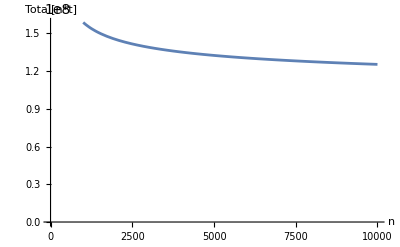

```mathematica
Plot[With[{a=2.,e=n/50, h=2000000.},With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}}, Simplify[Total[Table[18000000/Log10[glist[[i]]], {i, 8}]]]]], {n, 1000, 10000},PlotRange-> {0, Automatic}, AxesLabel-> {"n", "Total[n*t]"}]
```

The code below should be used when we don’t have a constant “c” but rather a c that depends upon the value of μ and on parameters η and θ

```mathematica
InverseSqrtMomentListsAlt[genetotals_,depthlist_, η_,θ_, n_]:=
With[{a =Max[2,Min[genetotals]],e=n/50, h= Max[genetotals]},
With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}},
With[{simEmatrix=KroneckerProduct[glist, depthlist]},MapThread[List, {glist, #}]&/@Transpose[Table[InverseSqrtFanoMoments[simEmatrix[[i]], √((η n)/glist[[i]]+ θ),n,Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))]],  {i, 1, Length[simEmatrix]}]]]]]
```

This revision speeds things up considerably, and it doesn’t need to call a separate InverseSqrtFanoMoments.  It has two forms, the one with fewer arguments takes a constant c

```mathematica
InverseSqrtMomentListsAltNew[genetotals_,depthlist_, c_, n_]:=
Module[{iter,cellmeans, simMat, invFanoMat,a =Max[2,Min[genetotals]],e=n/50, h= Max[genetotals]},
With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}},
Transpose[Table[
iter=Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))];
cellmeans=glist[[i]]*depthlist;
simMat=Map[RandomVariate[PoissonDistribution[#]]&,Transpose[RandomVariate[LogNormalDistribution[Log[#/(√(1+c^2))], √Log[1+c^2]],iter]&/@cellmeans] ,{2}];
invFanoMat =(1/(n-1)Total[ (#-cellmeans)^2/(cellmeans(1+c^2 cellmeans))]&/@simMat)^(-1/2);
{{ glist[[i]],Moment[#,2]},{glist[[i]],Moment[#,3]}, {glist[[i]],Moment[#,4]}, {glist[[i]],Moment[#,5]}}&@invFanoMat,{i, 8}]]] ];

InverseSqrtMomentListsAltNew[genetotals_,depthlist_, η_,θ_, n_]:=
Module[{j, iter,cellmeans, simMat, invFanoMat,a =Max[2,Min[genetotals]],e=n/50, h= Max[genetotals]},
With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}},
Transpose[Table[
j=((η n)/glist[[i]]+ θ);
iter=Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))];
cellmeans=glist[[i]]*depthlist;
simMat=Map[RandomVariate[PoissonDistribution[#]]&,Transpose[RandomVariate[LogNormalDistribution[Log[#/(√(1+j))], √Log[1+j]],iter]&/@cellmeans] ,{2}];
invFanoMat =(1/(n-1)Total[ (#-cellmeans)^2/(cellmeans(1+j cellmeans))]&/@simMat)^(-1/2);
{{ glist[[i]],Moment[#,2]},{glist[[i]],Moment[#,3]}, {glist[[i]],Moment[#,4]}, {glist[[i]],Moment[#,5]}}&@invFanoMat,{i, 8}]]] ]
```

Recall that θ and η are found by fitting the mean of the Pearson residuals (a[i]-μ[i])^2/(μ[i](1+j μ[i])) to 1.  Then we assume that the a[i] are taken from an NB distribution parametrized as NegativeBinomialDistribution[μ/(j μ),1/(1+j μ)].

```mathematica
InverseSqrtFanoMomentsListNB[genetotals_, depthlist_, η_, θ_, n_]:=
Module[{j, iter,cellmeans, simMat, invFanoMat,a =Max[2,Min[genetotals]],e=n/50, h= Max[genetotals]},
With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}},
Transpose[Table[
j=((η n)/glist[[i]]+ θ);
iter=Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))];
cellmeans=glist[[i]]*depthlist;
simMat = Transpose[RandomVariate[NegativeBinomialDistribution[#/(j #),1/(1+j #)],iter]&/@cellmeans];
invFanoMat =(1/(n-1)Total[ (#-cellmeans)^2/(cellmeans(1+j cellmeans))]&/@simMat)^(-1/2);
{{ glist[[i]],Moment[#,2]},{glist[[i]],Moment[#,3]}, {glist[[i]],Moment[#,4]}, {glist[[i]],Moment[#,5]}}&@invFanoMat,{i, 8}]]] ]
```

#### SqrtCorrectionmats

This takes the output of InverseSqrtMomentLists,  and generates four sets of correction matrices for use on the gene pair data.  These square matrices represent moments 2-5 of distributions under the null hypothesis of 1/(√(ϕ_a ϕ_b)) where a and b are the genes.  
Quiet is used because occasionally the genetotals are below 2 (i.e. just 1 UMI) yet our interpolation function does not go down to datapoints below 2.

```mathematica
SqrtCorrectionmats[invsqrtmoments_,genetotals_]:=
Quiet[Module[{
list2 = 10^Interpolation[Log10[invsqrtmoments[[1]]], InterpolationOrder->1][#]&/@Log10[genetotals],
list3 = 10^Interpolation[Log10[invsqrtmoments[[2]]], InterpolationOrder->1][#]&/@Log10[genetotals],
list4 = 10^Interpolation[Log10[invsqrtmoments[[3]]], InterpolationOrder->1][#]&/@Log10[genetotals],
list5 = 10^Interpolation[Log10[invsqrtmoments[[4]]], InterpolationOrder->1][#]&/@Log10[genetotals]},
{KroneckerProduct[list2, list2],KroneckerProduct[list3, list3],KroneckerProduct[list4, list4],KroneckerProduct[list5, list5]}]];
```

#### FanoCorrectionMatrices (to be dropped in Alt3 and Alt4)

This gives the Fano moment corrections for √ϕ for each gene, then uses KroneckerProduct to create three matrices for the combined correction for the product √(ϕ_a ϕ_b).  The three matrices represent the  3rd, 4th, and 5th moments of √(ϕ_a ϕ_b).  These are used to correct our correlation moments, which get divided by these.  The reason there is no 2nd moment matrix is that the moments for that are already built into the correlation coefficient moments; we can just substitute 1 for that.  The reason there is no 1st moment matrix is that the first correlation moment is zero, so there is no point in dividing it by anything  

Prior to 10/30/2020, we used the second version of the code, shown below as commented out.  However, the newer version is slightly more accurate.

```mathematica
(*FanoCorrectionMatrices[emat_, c_]:= 
Module[{n=Width[emat],χ=1+c^2},
{With[{𝒥3=√(n/(-1+n)^3 (n^2-n+Total/@((1+emat (-4+7 χ+6 (1-2 χ+χ^3) emat+(-3+6 χ-4 χ^3+χ^6)emat^2))/(emat (1+(-1+χ)emat)^2))))}, KroneckerProduct[𝒥3,𝒥3]],
With[{𝒥4=n/(n-1)+1/(-1+n)^2 Total/@((1+emat (-4+7 χ+6 (1-2 χ+χ^3) emat+(-3+6 χ-4 χ^3+χ^6) emat^2))/(emat (1+(-1+χ) emat)^2))}, KroneckerProduct[𝒥4,𝒥4]],
With[{𝒥5=√(1/(-1+n)^5(n^2+Total/@(-1+(1+emat (-4+7 χ+6 emat (1-2 χ+χ^3)+emat^2 (-3+6 χ-4 χ^3+χ^6)))/(emat (1+emat (-1+χ))^2))) (n^3+Total/@(1/(emat^2 (1+emat (-1+χ))^3)(1+emat (-9+31 χ)+2 emat^2 (16-57 χ+45 χ^3)+emat^3 (-56+180 χ-21 χ^2-168 χ^3+65 χ^6)+3 emat^4 (16-48 χ+14 χ^2+40 χ^3-6 χ^4-21 χ^6+5 χ^10)+emat^5 (-16+48 χ-24 χ^2-30 χ^3+12 χ^4+18 χ^6-3 χ^7-6 χ^10+χ^15)))+3 n Total/@(-1+(1+emat (-4+7 χ+6 emat (1-2 χ+χ^3)+emat^2 (-3+6 χ-4 χ^3+χ^6)))/(emat (1+emat (-1+χ))^2))))}, KroneckerProduct[𝒥5,𝒥5]]}]*)
```

#### CorrelationCumulants 5CF (to be dropped in Alt4)

This code finds the values of 4 cumulants. 
What it returns is a list of square matrices, starting with κ_2, in the form {κ_2, κ_3, κ_4...}

```mathematica
(*CorrelationCumulants5CF=Compile[{{ematrix, _Real, 2},{𝒥3, _Real, 2},{𝒥4, _Real, 2},{𝒥5,_Real, 2},{c,_Real},{n,_Real} },
{ConstantArray[1/n,{Length[ematrix], Length[ematrix]}],
(1/((n-1)^3 𝒥3))DotProductCF[(ematrix* (1+c^2 ematrix (3+c^2 (3+c^2)ematrix)))/((ematrix(1+c^2 ematrix))^(3/2)) , n] ,
(1/(n-1)^4)(-(3 (-1+n)^4)/n^3+1/𝒥4 DotProductCF[(1+ematrix (3+c^2 (7+ematrix (6+3 c^2 (6+ematrix)+c^4 (6+(16+15 c^2+6 c^4+c^6) ematrix)))))/(ematrix (1+c^2 ematrix)^2),n]),(-10/((-1+n)^3 n^2 𝒥3) DotProductCF[(1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)),n]+    (1/((n-1)^5 𝒥5)) DotProductCF[1/(ematrix^(3/2) (1+c^2 ematrix)^(5/2)) (1+ematrix (10+c^2 (15+ematrix (40+c^2 (75+60 ematrix+c^2 (25+10 (17+15 c^2+6 c^4+c^6) ematrix+(2+c^2) (15+60 c^2+81 c^4+62 c^6+29 c^8+8 c^10+c^12) ematrix^2)))))),n])}
, RuntimeAttributes->{Listable},Parallelization->True]*)
```

#### CorrelationCumulantsNewCF (added in Alt4)

This code finds the values of 4 cumulants and goes with the Alt3 form of BigSur.  The matrices ℱ2,  ℱ3, ℱ4, and ℱ5  are the output of InverseSqrtMomentLists.

What it returns is a list of square matrices, starting with κ_2, in the form {κ_2, κ_3, κ_4, κ_5}

```mathematica
CorrelationCumulantsNewCF=
Compile[{{ematrix, _Real, 2},{ℱ2, _Real, 2},{ℱ3, _Real, 2},{ℱ4, _Real, 2},{ℱ5,_Real, 2},{c,_Real},{n,_Real} },
{1/(-1+n)^2 ℱ2 n,
1/(-1+n)^3 ℱ3 DotProductCF[(1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)) , n],
1/(-1+n)^4(-3 n ℱ2^2  + ℱ4 DotProductCF[(1+ematrix (3+c^2 (7+ematrix (6+3 c^2 (6+ematrix)+c^4 (6+(16+15 c^2+6 c^4+c^6) ematrix)))))/(ematrix (1+c^2 ematrix)^2),n] ),

1/(-1+n)^5 (-10 ℱ2 ℱ3 DotProductCF[ (1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)) ,n] +ℱ5 DotProductCF[ 1/(ematrix^(3/2) (1+c^2 ematrix)^(5/2))(1+5 (2+3 c^2) ematrix+5 c^2 (8+15 c^2+5 c^4) ematrix^2+10 c^4 (6+17 c^2+15 c^4+6 c^6+c^8) ematrix^3+c^6 (30+135 c^2+222 c^4+205 c^6+120 c^8+45 c^10+10 c^12+c^14) ematrix^4),n])},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
CorrelationCumulantsNewCFAlt=
Compile[{{ematrix, _Real, 2},{ℱ2, _Real, 2},{ℱ3, _Real, 2},{ℱ4, _Real, 2},{ℱ5,_Real, 2},{c,_Real,1},{n,_Real} },
{1/(-1+n)^2 ℱ2 n,
1/(-1+n)^3 ℱ3 DotProductCF[(1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)) , n],
1/(-1+n)^4(-3 n ℱ2^2  + ℱ4 DotProductCF[(1+ematrix (3+c^2 (7+ematrix (6+3 c^2 (6+ematrix)+c^4 (6+(16+15 c^2+6 c^4+c^6) ematrix)))))/(ematrix (1+c^2 ematrix)^2),n] ),

1/(-1+n)^5 (-10 ℱ2 ℱ3 DotProductCF[ (1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)) ,n] +ℱ5 DotProductCF[ 1/(ematrix^(3/2) (1+c^2 ematrix)^(5/2))(1+5 (2+3 c^2) ematrix+5 c^2 (8+15 c^2+5 c^4) ematrix^2+10 c^4 (6+17 c^2+15 c^4+6 c^6+c^8) ematrix^3+c^6 (30+135 c^2+222 c^4+205 c^6+120 c^8+45 c^10+10 c^12+c^14) ematrix^4),n])},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
CorrelationCumulantsNB=
Compile[{{ematrix, _Real, 2},{ℱ2, _Real, 2},{ℱ3, _Real, 2},{ℱ4, _Real, 2},{ℱ5,_Real, 2},{c,_Real,1},{n,_Real} },
With[{ξ = c^2}, 
{n/(n-1)^2 ℱ2,
ℱ3/(n-1)^3 DotProductCF[(1+2 ξ ematrix)/(√(ematrix (1+ξ ematrix))),n],
ℱ4/(n-1)^4(-3 n (3 ℱ2^2)/ℱ4+DotProductCF[(1+3 (1+2 ξ) ematrix (1+ξ ematrix))/(ematrix (1+ξ ematrix)),n]), 
ℱ5/(n-1)^5(
DotProductCF[((1+2 ξ ematrix) (1+2 (5+6 ξ)ematrix (1+ξ ematrix)))/(ematrix (1+ξ ematrix))^(3/2),n]-10(ℱ2 ℱ3)/ℱ5 DotProductCF[ (1+2 ξ ematrix)/(√(ematrix (1+ξ ematrix))),n])}
],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

#### CornishFisherPolynomialCoefficients 5CF

Rather than try to generate the intact polynomials, this code just returns their coefficients as a list of matrices.  The matrices go in order from the coefficients of lowest to highest order, i.e. a+ bx +cx^2+dx^3, etc.  
Note, a small error in the code for 5CF was fixed on 10/30/2022

```mathematica
CornishFisherPolynomialCoefficients5CF=
Compile[{{κ2, _Real, 2}, {κ3, _Real, 2},{κ4, _Real, 2},{κ5, _Real, 2}, {cc, _Real, 2}},
{-cc-κ3/(6 κ2)+(17 κ3^3)/(324 κ2^4)-(κ3 κ4)/(12 κ2^3)+κ5/(40 κ2^2), (√κ2+(5 κ3^2)/(36 κ2^(5/2))-κ4/(8 κ2^(3/2))), (κ3/(6 κ2)-(53 κ3^3)/(324 κ2^4)+(5 κ3 κ4)/(24 κ2^3)-κ5/(20 κ2^2)),(-κ3^2/(18 κ2^(5/2))+κ4/(24 κ2^(3/2))),(κ3^3/(27 κ2^4)-(κ3 κ4)/(24 κ2^3)+κ5/(120 κ2^2))}, RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

Note that κ2 is simply 1/n, as pointed out above.

#### FastFindX (to be dropped in Alt4)

The first part of the code, TestRoot, is just a version of FindRoot that looks only at positive numbers for positive correlations and negative numbers for negative correlations.  If the zero-order term of the CF polynomial is within “threshold” of zero, it just returns zero.  If FindRoot fails to find anything, or generates any error message at all, it returns “z”.  

FastFindX  starts off by applying FindRoot to a whole set of CF parameters.  Then it locates those positions where z was returned. 
To those positions, it tries FindInstance.  This is necessary because there are some cases where FindRoot will generate an error message even though a root can be found, and thus a z will be returned instead of the actual root.  Where FindInstance fails, it returns “x”.  The results of this step are then incorporated into the list of results replacing all the z’s. 

Finally, the code retrieves all the positions where “x” appears, and tries a version of FindInstance that checks for a location where the slope is zero and the curvature is either positive or negative, depending on whether the zero-order term of the polynomial is positive or negative.  Essentially this gives us locations where the CF curve comes close to the x-axis but doesn’t quite cross it.  These values are then used to replace all the x-values.  

We find empirically that, when all three steps are completed, no x-values remain.

```mathematica
(*TestRoot[params_, threshold_]:=
If[ Abs[First[params]]<threshold, 0.,
Quiet[If[Last[params]==1,
			 Check[x/.FindRoot[params.{1, x,x^2,x^3,x^4,0}==0, {x, 0,0,∞ },Method->"Secant"],z],
		Check[x/.FindRoot[params.{1, x,x^2,x^3,x^4,0}==0, {x, 0,-∞,0 },Method->"Secant"],z]]]]*)
```

```mathematica
(*FastFindX[paramset_, threshold_]:=
Module[{r1 ,r2,failposns1,failposns2,  fixedfails1, fixedfails2},
r1=TestRoot[#, threshold]&/@paramset;
Print["Stage 1 of FindX complete", TimeObject[Now]];
failposns1= Flatten[Position[r1, z]];
(*this gives you the locations within r1 where TestRoot failed; r1 has the same length as paramset*);
fixedfails1 =Flatten[x/.FindInstance[Evaluate[#.{1, x,x^2,x^3,x^4,0}==0]&&Sign[x]== Sign[Last[#]] ,x,Reals]&/@paramset[[failposns1]]];
(*this gives substitute values for each of the failed positions in r1; where it doesn't it puts an x.  we can thread failposns1 onto fixedfails1 and generate replacement rules for r1*);
r2 =ReplacePart[r1,Thread[failposns1-> fixedfails1]] ;
Print["Stage 2 of FindX complete", TimeObject[Now]];
failposns2 = Flatten[Position[r2, x]];
(*this gives the positions within r2, and within paramset, where a result was not yet found*);
fixedfails2=Flatten[x/.FindInstance[Evaluate[(#.{0, 1,2x,3 x^2,4 x^3,0}==0&&Sign[First[#]]*#.{0, 0,2,6x,12 x^2,0}>0)], x, Reals]&/@paramset[[failposns2]]];
(*this gives substitute values for each of the failed positions; however we need to know their positions in r1*);
ReplacePart[r2,Thread[failposns2-> fixedfails2]]]*)
```

#### NewFindX and ImprovedFindX (added in Alt4)

First we generate some code that NewFindX calls :
Both of them first identify x-boundary values equal to plus or minus √2 InverseErfc[2. 10^-cutoff], which are the x-values corresponding to a particular p-value threshold.

QuickTest6CF returns a zero if the signs at the xboundary values are different, or the sign at x=0 is different from at the positive x-boundary value, and 1 otherwise.  Note that the following function might run faster, provided that ContainsAll can be compiled.

If[ContainsAll[Table[Sign[a+b x+c x^2+d x^3+e x^4], {x, {-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}}],{-1,1}],0,1]

If ContainsAll cannot be compiled we can simply apply this transformation to the table:
Multiply all the terms, sum all the terms, multiply that together, and take the absolute value.   If the answer if 6 (because there are six parts in the table) then the signs of all size were either 1 or -1 and  therefore there is no root  (so output 1), for example:

```mathematica
QuickTest6CF =  Compile[{{a, _Real},{b, _Real},{c, _Real},{d, _Real},{e, _Real}, {cutoff, _Real}},With[{x=√2 InverseErfc[2. 10^-cutoff]},
Which[
Sign[(a-b x+c x^2-d x^3+e x^4) (a+b x+c x^2+d x^3+e x^4)]== -1,0,
Sign[a (a+b x+c x^2+d x^3+e x^4)]== -1,0,True, 1]],RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

```mathematica
QuickTest6CFAlt=Compile[{{a, _Real},{b, _Real},{c, _Real},{d, _Real},{e, _Real}, {cutoff, _Real}},With[{k=√2 InverseErfc[2. 10^-cutoff]},If[Abs[Total[Table[Sign[a+b x+c x^2+d x^3+e x^4], {x, {-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}}]]]==7,1,0]], RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

This much faster version takes the whole parameters list as one argument, and the Table of  {x, {-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}} as its second.  So one has to generate the table first;

```mathematica
QuickTest6CFAltNew=
Compile[{{paramslist, _Real, 2}, {table, _Real,2}},
Abs[Total[#]]&/@Outer[Sign[Dot[#1,#2]]&,paramslist,table ,1],RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

```mathematica
SecondTestCF=Compile[{{a, _Real},{b, _Real},{c, _Real},{d, _Real},{e, _Real}, {cutoff, _Real}},With[{x=√2 InverseErfc[2. 10^-cutoff]},
Which[
Sign[b-2 c x+3 d x^2-4 e x^3]==-1,1,(*if the slope at -X isn't positive we keep*)
Sign[b+2 c x+3 d x^2+4 e x^3]==-1,0,(*if the slope at X is negative we reject*)
3 d^2<8 c e,1,(*if there is no inflection point we keep*)
-x<(3 d-√(9 d^2-24 c e))/(12 e)<x &&Sign[45 d^3-36 c d e-15 d^2 √(9 d^2-24 c e)+8 e (9 b e-c √(9 d^2-24 c e)) ]==-1,0,(*if the location of the first inflection point is in [-X,X] AND the slope at that point is negative, we reject*)
-x<(3 d+√(9 d^2-24 c e))/(12 e)<x &&  Sign[45 d^3-36 c d e+15 d^2 √(9 d^2-24 c e)+8 e (9 b e+c √(9 d^2-24 c e))]==-1,0,(*otherwise, if the location of the second inflection point is in [-X,X] AND  slope at that point is negative, we reject*)
True,1 (*otherwise we keep*)]],
RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

```mathematica
FixedFirst[list_]:= If[Length[list]>0, First[list]];
FixedLast[list_]:= If[Length[list]>0, Last[list]];
```

```mathematica
SmallerInterval[list_]:=
If[
Abs[Last[First[list]]]<Abs[First[Last[list]]],First[list], Last[list]]
```

```mathematica
Foundroots[params_]:=
With[{eqn =params.{1, x, x^2, x^3, x^4,0} },
With[{list= N@First[RootIntervals[eqn]]},
With[{spanningset =Select[list,  Sign[Times[First[#],Last[#]]]==-1&] },
Which[
Length[spanningset]>0, 
x/.FindRoot[eqn, Flatten[{x, spanningset}], Method->"Secant"],
Length[list]==0, 
z, 
Length[list]==1,
x/.FindRoot[eqn, Flatten[{x, list}], Method->"Secant"],
True, 
x/.FindRoot[eqn, Flatten[{x, Flatten@SmallerInterval[{FixedLast@Select[list, Last[#]<0&],FixedFirst@Select[list, First[#]>0&]}/.Null-> Nothing]}], Method-> "Secant"] ]
]]]
```

The alternative code uses NRoots and is simpler and faster

```mathematica
FoundrootsAlt[params_]:= Flatten[TakeSmallestBy[(x/.{ToRules[NRoots[#,x]]}/._Complex-> z), Abs,1]&/@(#.{1, x, x^2, x^3, x^4,0}==0&/@params)]
```

```mathematica
FindZ[augmentedParams_]:=
With[{rootrules=Select[NSolve[0==augmentedParams.{0,1,2 x,3 x^2,4 x^3,0},x], Im[x/.#]==0&]}, 
With[{vals=Chop[augmentedParams.{1, x, x^2, x^3, x^4,0}/.rootrules]},
x/.rootrules[[First[Ordering[Abs[vals]]]]]]]
```

The alternative code uses NRoots and is simpler and faster

Here the syntax for FindZAlt is that it operates on the entire parameters list, not just one at a time.  so we write FindZAlt[paramslist] rather than FindZAlt/@params.

```mathematica
FindZAlt[paramslist_]:=Flatten[TakeSmallestBy[#, Abs, 1]&/@(x/.{ToRules[#]}&/@(NRoots[#,x]&/@((0==#.{0,1,2 x,3 x^2,4 x^3,0})&/@paramslist))/._Complex-> Nothing)]
```

The equation below finds positions in paramslist where the second derivative is zero.

```mathematica
FindW[paramslist_]:=
Flatten[Position[(x/.Solve[#.{0, 0, 2, 6x, 12 x^2,0}==0,x]&/@paramslist)/._Complex-> Nothing, x_/;Length[x]>0]]
```

Here are the steps.

We begin with a list of augmented parameters of length Binomial[m,2].  Let use define -X and X as the X-positions corresponding to our p-value cutoff.  

Step 1:  We apply QuickTest6CF to all the augmented parameters to generate a list of positions called “posns1” where QuickTest6CF returns 1.  The indexing of posns1 runs from 1 to Binomial[m,2].   QuickTest6CF is a fast function that takes as input a list of augmented parameters, and a -logpvalue cutoff, and outputs 1 or 0 to indicate whether the values of the polynomial at x= -X and x=X are different, or whether the values at x= -X and x= X have the same sign, but one that is different from the value at x=0.   If they do then, by continuity we know that there is a root between -X and X, i.e. a root that will produce a -logp-value below the cutoff.   So our first step is to identify all the polynomials that cannot be excluded on these grounds.  

Step 2:  We know that gene pair correlations involving very lowly expressed genes sometimes don’t display an actual root between -X and X, but come close to doing so, and should be excluded from further consideration whenever that happens.  We call that having a “quasiroot”.   Empirically, we find that this happens when the maximum gene expression in the pair is <0.05 (given 1662 cells), i.e. when the total UMI in the most highly expressed gene amounts to less than 84.  So we need to find the positions in our augmented parameters list where there is a quasiroot.  

First we generate a Sparse Matrix of just gene pairs where the maximum gene expression meets that criterion, and then use ListIndex to convert the Explicit Positions to list indices.  We then use that to divide the positions from the previous step into two groups, “posns1high” and “posns1low” for gene expression.  We then take the posns1low and apply SecondTestCF.  This test does a series of things:
	1) If the slope at -X isn’t positive, there isn’t a quasiroot (we find empirically that the slope at -X is always positive, but we check anyway)
	2) Then, if the slope at X is negative it guarantees a maximum between -X and X, which we take to be a quasiroot,
	3) If either of the only possible inflection points (the positions of which can be solved for analytically as (3 d-√(9 d^2-24 c e))/(12 e) and (3 d+√(9 d^2-24 c e))/(12 e) ) lies between -X and X, if the slope at either of them is negative then there must have been a maximum between -X and X.  Note that the slopes at each of these points are (45 d^3-36 c d e-15 d^2 √(9 d^2-24 c e)+8 e (9 b e-c √(9 d^2-24 c e)))/(72 e^2) and (45 d^3-36 c d e+15 d^2 √(9 d^2-24 c e)+8 e (9 b e+c √(9 d^2-24 c e)))/(72 e^2), however in testing their signs we may exclude the 72 e^2 in the denominator because, being a square it is necessarily positive so it has no influence on the sign.  
	
Step 3:  We define posns2 as the union of posns1high and those elements of posns1low that passed the slope and intercept tests.  The indexing of these still runs from 1 to Binomial[m,2]

Step 4:  We apply Foundroots to augmentedParameters[[posns2]].  This finds roots except where no true roots exist in which case it returns z.  
	To those cases where no root was  found, we use FindZ to return a quasi-root.  We then replace the z’s with these quasiroots; the whole thing together is called rootsComplete.  This list has the same length as posns2.  Thus if we want to find out which augmented parameters go with which roots we match them up with augmentedparameters[[posns2]].
	
Step 5:  We use Benjamini Hochberg to find the significance cutoff for FixedPValFunc/@rootsComplete, using Binomial[m,2] as our Array length.   We define checkposns as those locations within rootsComplete where the BH cutoff was exceeded.  In order to get this indexing back to that of augmentedparameters we take posns2[[checkposns]]
Step7:  We now want to search for additional quasiroots, at those check-positions, where the quasiroot falls below the BH cutoff.  We remove any of those as well from the list.  Finally, we index the list by augmentedparameters[[posns2]]

```mathematica
NewFindX[augmentedParameters_,cutoff_, genetotals_, alpha_]:=
Module[{ passedTest,passedTest2,lowposns,posns1low, posns1high,posns2,  trueroots, rootsComplete,logpcriterion, checkposns,additionalQuasirootsPosns, rootsFinal},
(*step 1*)
passedTest=
With[{table=Table[{1, x,x^2,x^3, x^4,0}, {x,{-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}}]/.k-> √2 InverseErfc[2. 10^-cutoff]},Flatten[SparseArray[BoolEval[QuickTest6CFAltNew[augmentedParameters, table]==7]]["ExplicitPositions"]]];
Flatten[SparseArray[QuickTest6CF[#1, #2, #3, #4, #5, cutoff]&@@#&/@augmentedParameters]["ExplicitPositions"]];
Print["First quick test complete.  Surviving parameter sets = ", Length[passedTest], TimeObject[Now]];
(*step 2*)
lowposns=ListIndex/@(SparseArray[LowerTriangularize[KroneckerProduct[SparseArray[BoolEval[genetotals<84]], SparseArray[BoolEval[genetotals<84]]],-1]]["ExplicitPositions"]);
posns1low = Intersection[passedTest, lowposns];
posns1high = Complement[passedTest, lowposns];
passedTest2=SecondTestCF[#1, #2, #3, #4, #5, cutoff]&@@#&/@augmentedParameters[[posns1low]];
(*step3*)
posns2=Union[
If[passedTest2=={},{},
posns1low[[Flatten[SparseArray[passedTest2]["ExplicitPositions"]]]]], 
posns1high];
Print["Second quick test complete.  Surviving parameter sets = ",Length[posns2],TimeObject[Now]];
(*step 4*)
trueroots =  Foundroots/@augmentedParameters[[posns2]];
Print["True roots found",TimeObject[Now]];
rootsComplete=ReplacePart[trueroots, Thread[Flatten[Position[trueroots, z]]-> FindZ/@augmentedParameters[[posns2]][[Flatten[Position[trueroots, z]]]]]];
(*step 5*)
logpcriterion=-Log10@BHNew[10^-(FixedPValFunc/@rootsComplete),alpha,Binomial[Length[genetotals],2] ];
Print["p criterion = ",ScientificForm[10^-logpcriterion],TimeObject[Now]];
checkposns=
Flatten@Position[FixedPValFunc/@rootsComplete, x_/;x> logpcriterion];
additionalQuasirootsPosns=posns2[[checkposns[[Flatten[Position[FixedPValFunc/@(FindZ/@augmentedParameters[[posns2[[checkposns]]]]), x_/;x<logpcriterion]]]]]];
rootsFinal=ReplacePart[rootsComplete,additionalQuasirootsPosns-> 0];
SparseArray[Thread[posns2-> rootsFinal], Length[augmentedParameters]]
]
```

```mathematica
NewFindXAlt[augmentedParameters_,cutoff_, genetotals_, alpha_]:=
Module[{ passedTest,passedTest2,lowposns,posns1low, posns1high,posns2,  trueroots, rootsComplete,logpcriterion, checkposns,additionalQuasirootsPosns, rootsFinal},
(*step 1 generates the positions where a quick test is passed*)
passedTest=Flatten[SparseArray[QuickTest6CFAlt[#1, #2, #3, #4, #5, cutoff]&@@#&/@augmentedParameters]["ExplicitPositions"]];
Print["First quick test complete.  Surviving parameter sets = ", Length[passedTest], TimeObject[Now]];
(*step 2*)
lowposns=ListIndex/@(SparseArray[LowerTriangularize[KroneckerProduct[SparseArray[BoolEval[genetotals<84]], SparseArray[BoolEval[genetotals<84]]],-1]]["ExplicitPositions"]);
posns1low = Intersection[passedTest, lowposns];
posns1high = Complement[passedTest, lowposns];
passedTest2=SecondTestCF[#1, #2, #3, #4, #5, cutoff]&@@#&/@augmentedParameters[[posns1low]];
(*step3*)
posns2=Union[If[passedTest2=={},{},
posns1low[[Flatten[SparseArray[passedTest2]["ExplicitPositions"]]]]], posns1high];
Print["Second quick test complete.  Surviving parameter sets = ",Length[posns2],TimeObject[Now]];
(*step 4*)
trueroots =  Foundroots/@augmentedParameters[[posns2]];
Print["True roots found",TimeObject[Now]];
rootsComplete=ReplacePart[trueroots, Thread[Flatten[Position[trueroots, z]]-> FindZ/@augmentedParameters[[posns2]][[Flatten[Position[trueroots, z]]]]]];
(*step 5*)
logpcriterion=-Log10@BHNew[10^-(FixedPValFunc/@rootsComplete),alpha,Binomial[Length[genetotals],2] ];
Print["p criterion = ",ScientificForm[10^-logpcriterion],TimeObject[Now]];
checkposns=
Flatten@Position[FixedPValFunc/@rootsComplete, x_/;x> logpcriterion];
additionalQuasirootsPosns=posns2[[checkposns[[Flatten[Position[FixedPValFunc/@(FindZ/@augmentedParameters[[posns2[[checkposns]]]]), x_/;x<logpcriterion]]]]]];
rootsFinal=ReplacePart[rootsComplete,additionalQuasirootsPosns-> 0];
SparseArray[Thread[posns2-> rootsFinal], Length[augmentedParameters]]
]
```

```mathematica
ImprovedFindXAlt[augmentedParameters_,cutoff_, genetotals_, alpha_]:=
Module[{ table, passedTest,survivingparams, trueroots,rootsComplete,logpcriterion, checkposns,additionalQuasirootsPosns, rootsFinal},
table=Table[{1, x,x^2,x^3, x^4,0}, {x,{-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}}]/.k-> √2 InverseErfc[2. 10^-cutoff];
passedTest=Flatten[SparseArray[BoolEval[QuickTest6CFAltNew[augmentedParameters, table]==7]]["ExplicitPositions"]];
survivingparams= augmentedParameters[[passedTest]];
Print["Quick test complete.  Surviving parameter sets = ", Length[passedTest], TimeObject[Now]];
trueroots =  Flatten[TakeSmallestBy[(x/.{ToRules[NRoots[#,x]]}/._Complex-> z)/.{z->Nothing}, Abs,1]&/@(#.{1, x, x^2, x^3, x^4,0}==0&/@survivingparams)];
Print["True roots found",TimeObject[Now]];
rootsComplete=ReplacePart[trueroots, Thread[Flatten[Position[trueroots, z]]-> FindZAlt[survivingparams[[Flatten[Position[trueroots, z]]]]]]];
Print["Quasiroots found ",TimeObject[Now]];
SparseArray[Thread[passedTest-> rootsComplete], Length[augmentedParameters]]
]
```

Here are the steps.
We begin with a list of augmented parameters of length Binomial[m,2].  Let use define -X and X as the X-positions corresponding to our p-value cutoff.  

Step 1:  We apply QuickTest6CF to all the augmented parameters to generate a list of positions, “passedTest” where QuickTest6CF returns 1.  The indexing of passedTest runs from 1 to Binomial[m,2].   QuickTest6CF is a fast function that takes as input a list of augmented parameters, and a -logpvalue cutoff, and outputs 1 or 0 to indicate whether the values of the polynomial at x= -X and x=X are different, or whether the values at x= -X and x= X have the same sign, but one that is different from the value at x=0.   If they do then, by continuity we know that there is a root between -X and X, i.e. a root that will produce a -logp-value below the cutoff.   So our first step is to identify all the polynomials that cannot be excluded on these grounds.  

Step 2:  We then apply NRoots to the surviving parameter sets (survivingparams), taking the Real one with the smallest absolute value. Where no true root exist it returns z.  

Step 3: To those cases where z was  returned, we use FindZAlt to return a quasi-root.  We then replace the z’s with these quasiroots; the whole thing together is called rootsComplete.  This list has the same length as passedTest.  Thus if we want to find out which augmented parameters go with which roots we match them up with survivingparams.
	
Step 4:  We use Benjamini Hochberg to find the significance cutoff for FixedPValFunc/@rootsComplete, using Binomial[m,2] as our Array length.   We define checkposns as those locations within rootsComplete where the BH cutoff was exceeded, i.e. those positions that are significant given our choice of alpha.  

Step5:  We no longer search for additional quasiroots, as analysis suggests there are few if any cases that appear clearly significant but aren’t because they have a quasiroot that falls in the insignificant zone.

#### InferredPCCs

This operates on a matpac and on the output matrix with negative log p-values.  It produces a matrix of p-value-correlated correlations.  It calls a code that uses the Fisher p-value formula to give an equivalent correlation coefficient based on the p-value and the vector length.  

Because it is relatively slow, it first prunes the pvalue matpac to set any values less than or equal to “cutoff” to zero.  If necessary we can adjust this to a lower number using an option.

```mathematica
InferredPCCs[logpvalmatrix_,pccSignmatrix_, cutoff_, n_]:= 
Module[{mat=SparseArray[logpvalmatrix*BoolEval[logpvalmatrix>cutoff],Dimensions[logpvalmatrix]]},
SparseArray[pccSignmatrix *Tanh[(√2 InverseErfc[ 10^-mat])/(√(-3.+n))], Dimensions[mat]]]
```

Note that if we are going to use versions of BigSur that do not collect pvalues below 10^-20, then the maximum PCC they can produce is

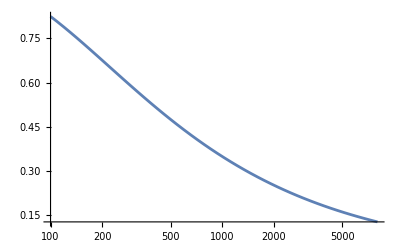

```mathematica
LogLinearPlot[Tanh[(√2 InverseErfc[ 10^-30])/(√(-3.+n))], {n, 100, 8000}]
```

But we know when x is large   Erfc[z]~  e^(-z^2), which enables us to approximate

```mathematica
Solve[f == ⅇ^(-z^2), z]
```

{{z→ConditionalExpression[-√(2 ⅈ π C[1]+Log[1/f]), C[1]∈ℤ]},{z→ConditionalExpression[√(2 ⅈ π C[1]+Log[1/f]), C[1]∈ℤ]}}

InverseErfc[y]~√Log[1/y]

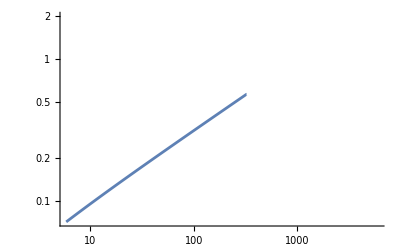
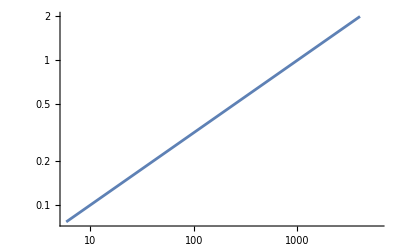

```mathematica
LogLogPlot[#, {i, 0, 6000}, PlotRange-> {{0,6000},{0,2}}]&/@{(√2 InverseErfc[ 10^-i])/(√(-3.+4655)),(√(2 Log[ 10]))/(√(-3.+4655))√i }
```

So the InverseErfc can be approximated, and now we can put this into Tanh

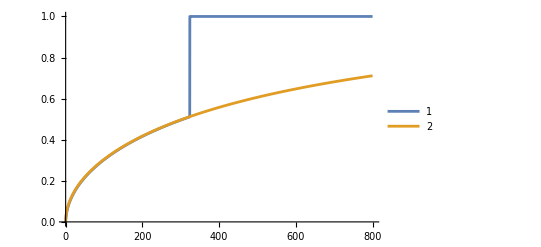

```mathematica
With[{n=4655},Plot[{Tanh[(√2 InverseErfc[ 10^-i])/(√(-3.+n))],Tanh[(√(2 Log[ 10]))/(√(-3.+n))√i]}, {i, 0, 800}, PlotLegends-> {1, 2}]]
```

```mathematica
InferredPCCs2[logpvalmatrix_,pccSignmatrix_, cutoff_, n_]:= 
Module[{mat=SparseArray[logpvalmatrix*BoolEval[logpvalmatrix>cutoff],Dimensions[logpvalmatrix]], sa,be, mat2, sa2},
sa=SparseArray[pccSignmatrix *Tanh[(√2 InverseErfc[ 10^-mat])/(√(-3.+n))], Dimensions[mat]];
be=BoolEval[Abs[sa]==1];
mat2 = SparseArray[logpvalmatrix*be];
sa2 =SparseArray[pccSignmatrix *Tanh[ (√(2 Log[ 10]))/(√(-3.+n))√mat2]] ;
sa+sa2-sa*be]
```

#### CreateGNO

```mathematica
CreateGNO[matpac_,sigpccmatrix_]:= 
Module[{ hits},
hits=Sort[Union[Flatten[Keys[Drop[ArrayRules[sigpccmatrix],-1]]]]];
If[Length[ArrayRules[sigpccmatrix]]<2,Print["no hits found"],
{BoolEval[Abs[sigpccmatrix]⟦hits, hits⟧>0],
matpac⟦2, hits⟧, 
sigpccmatrix⟦hits, hits⟧, 
"Metadata"->{"From Expression Matrix"-> "Metadata"/.Last[matpac]}}]]
```

```mathematica
CreateGNO[matpac_,sigpccmatrix_,logpvalmat_, pvalcutoff_]:=
Module[{hits, adjustedmatrix},
adjustedmatrix=SparseArray[sigpccmatrix*BoolEval[logpvalmat>-Log10[pvalcutoff]],Dimensions[sigpccmatrix]];
hits=Sort[Union[Flatten[Keys[Drop[ArrayRules[adjustedmatrix],-1]]]]];
If[Length[ArrayRules[adjustedmatrix]]<2,Print["no hits found"],
{BoolEval[Abs[adjustedmatrix]⟦hits, hits⟧>0],
matpac⟦2, hits⟧, 
adjustedmatrix⟦hits, hits⟧, 
"Metadata"->{"From Expression Matrix"-> "Metadata"/.Last[matpac], "Imposed p-value cutoff of "<>ToString[pvalcutoff]}}]]
```

```mathematica
CreateGNO[matpac_,sigpccmatrix_,poslogpvalmat_,neglogpvalmat_, pvalcutoff_]:=
Module[{hits, adjustedmatrix},
adjustedmatrix=SparseArray[sigpccmatrix*BoolEval[poslogpvalmat+neglogpvalmat>-Log10[pvalcutoff]],Dimensions[sigpccmatrix]];
hits=Sort[Union[Flatten[Keys[Drop[ArrayRules[adjustedmatrix],-1]]]]];
If[Length[ArrayRules[adjustedmatrix]]<2,Print["no hits found"],
{BoolEval[Abs[adjustedmatrix]⟦hits, hits⟧>0],
matpac⟦2, hits⟧, 
adjustedmatrix⟦hits, hits⟧, 
"Metadata"->{"From Expression Matrix"-> "Metadata"/.Last[matpac], "Imposed p-value cutoff of "<>ToString[pvalcutoff]}}]]
```

#### TruncateGNO

This truncates a gNO, eliminating correlations that fall below a certain threshold of PCC.  Options allow one to also select only the positive or negative correlations .  
If the second argument is left out, only the options are applied

```mathematica
Options[TruncateGNO]={"Positive Only"-> False, "Negative Only"-> False};

TruncateGNO[gNO_, ccthreshold_:0, OptionsPattern[]]:= 
Module[{hits, sigmat, adjustedmatrix},
sigmat=Which[OptionValue["Positive Only"],BoolEval[gNO[[3]]>ccthreshold], OptionValue["Negative Only"],BoolEval[-gNO[[3]]>ccthreshold], True, BoolEval[Abs[gNO[[3]]]>ccthreshold]];
If[Length[ArrayRules[sigmat]]<2, Print["no hits found"];Abort[]];
adjustedmatrix=SparseArray[sigmat*gNO[[3]], Dimensions[gNO[[3]]]];
hits=Sort[Union[Flatten[Keys[Drop[ArrayRules[adjustedmatrix],-1]]]]];
{BoolEval[adjustedmatrix⟦hits, hits⟧>0],gNO[[2, hits]],adjustedmatrix⟦hits, hits⟧, 
"Metadata"->{"From Expression Matrix"-> "Metadata"/.Last[gNO], "Imposed Abs[cc] cutoff of "<>ToString[ccthreshold]}}
];
```

#### GeneSubsetGNO

This cuts down a GNO to contain only certain genes.  If the list contains genes that are not in the gNO they are ignored.  

We are adding an option to this:  When it is set to “Purge”-> True, it will purge from the gNO any genes for which there are no correlations.  Normally this is set to False, but for some applications, like NewPlot we need it set to True

Note that it was noticed on 3/13/23 that with the original form of this function, unless the genes were put in the same order as they appear in the gNO, the resulting matrix would come out not properly lower-triangularized.  All the data were present but sometimes whether it appeared in mainly in column or row varied.  This got fixed by restoring the symmetry and then lower triangularizing.  It didn’t seem to affect any downstream functions.  

If none of the genes in the subset are found in the gNO, then an error will occur the first time it reaches gNO[[1,hits, hits]].  To prevent this, we insert an IF statement at the beginning, that allows it to generate an empty matrix in this event.

```mathematica
Options[GeneSubsetGNO]={"Purge"-> False};
GeneSubsetGNO[gNO_, genes_, OptionsPattern[]]:=
If[Intersection[genes, gNO[[2]]]=={},{{},{},{},"Metadata"-> "list was empty"},
Module[{hits = Flatten[Position[gNO[[2]],#]&/@genes],tempgNO, newhits},
tempgNO={LowerTriangularize[RestoreSymmetryExceptDiagonal[gNO[[1,hits, hits]]],-1], gNO[[2, hits]],LowerTriangularize[RestoreSymmetryExceptDiagonal[gNO[[3, hits, hits]]],-1]};
If[OptionValue["Purge"],
newhits =Union[Flatten[tempgNO[[1]]["ExplicitPositions"]]];
{tempgNO[[1, newhits, newhits]], tempgNO[[2, newhits]], tempgNO[[3, newhits, newhits]],"Metadata"->{"From GNO"-> "Metadata"/.gNO[[4]], "Having subsetted "<>ToString[Length[newhits]]<>" genes"} },
Append[tempgNO, "Metadata"->{"From GNO"-> "Metadata"/.gNO[[4]], "Having subsetted "<>ToString[Length[hits]]<>" genes"}]]]]
```

#### FindBestC (older method for finding C)

This finds the best C-value to use for BigSur; it generates a plot, and where the plot crosses zero is typically the best choice.  The “depthscaling” argument can be “Auto” if one wants the depthlist calculated automatically.  
If this is used, then when using BigSur one can set the option “Interrupt” to False.
The second version of this allows one to give the resulting plot a title.

```mathematica
FindBestC[matpac_, depthscaling_]:= 
Module[{n,m, mat,genetotals, depthlist, ematrix},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
n=Width[mat];
m=Length[genetotals];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
ListPlot[Table[{c,a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat,  1/(n-1)Total/@(((mat-ematrix)/(√(ematrix(1+c^2 ematrix))))^2)}],-2<First[#]<1&],a x+b,{a,b},x]}, {c,0,0.8,0.05}], GridLines-> Automatic]]
```

```mathematica
FindBestC[matpac_, depthscaling_, title_]:= 
Module[{n,m, mat,genetotals, depthlist, ematrix},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
n=Width[mat];
m=Length[genetotals];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
ListPlot[Table[{c,a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat,  1/(n-1)Total/@(((mat-ematrix)/(√(ematrix(1+c^2 ematrix))))^2)}],-2<First[#]<1&],a x+b,{a,b},x]}, {c,0,0.8,0.05}], GridLines-> Automatic, PlotLabel-> title]]
```

#### FindBestCAlt (added in Alt4, uses log-log space, probably better)

```mathematica
FindBestCAlt[matpac_, depthscaling_]:= 
Module[{n,m, mat,genetotals, depthlist, ematrix},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
n=Width[mat];
m=Length[genetotals];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
ListPlot[Table[{c,a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat, Log10[ 1/(n-1)Total/@(((mat-ematrix)/(√(ematrix(1+c^2 ematrix))))^2)]}],-1<First[#]<2&],a x+b,{a,b},x]}, {c,0,0.8,0.05}], GridLines-> Automatic]]
```

#### BigSurAlt2

CFthreshold sets a threshold for the zero order term of the Cornish Fisher Polynomial, enabling us to filter out cases where the CornishFisher gets it wrong by putting the y-intercept on the wrong side of the x-axis.  See FastFindX for details.

```mathematica
Options[BigSurAlt2]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"CFThreshold"->0.026, "SigBinWidth"-> 0.05,"Interrupt"-> True };

BigSurAlt2[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,logpmatrix,equivalentPCCs, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
Print["mcFano slope between 0.01 and 10 is ",a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat, mflist}],-2<First[#]<1&],a x+b,{a,b},x]];
If[OptionValue["Interrupt"],Print["Continue or try a different value of c?"];Interrupt[]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=FanoCorrectionMatrices[ematrix, c];
Print["Moment corrections for √ϕ_a acquired and saved",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
Print["Matrix of PCC directions acquired",TimeObject[Now]];
ccmats=CorrelationCumulants5CF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=FastFindX[augmentedParameters, OptionValue["CFThreshold"]]; 
Print["x-values acquired",TimeObject[Now]];
logpmatrix=ListToSymmetricMatrix[FixedPValFunc/@xlist];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,significantPCCmatrix];
Export[filemarker<>"_gNO.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]];
SetDirectory[NotebookDirectory[]];
Label[end];
Print["done"]; Beep[]
];
```

#### BigSurAlt3

Here we use the proper matrix corrections for the square roots of the Fano factors.  
We  add in an option, “Fano Inverse Sqrt Correction”, however, to block the generation of these when we set it to False, in case we want to see whether the results come out the same.

```mathematica
Options[BigSurAlt3]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Correction"-> True,"CFThreshold"->0.026, "SigBinWidth"-> 0.05,"Interrupt"-> True };

BigSurAlt3[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,invsqrtmoments,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,logpmatrix,equivalentPCCs, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
Print["mcFano slope between 0.01 and 10 is ",a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat, mflist}],-2<First[#]<1&],a x+b,{a,b},x]];
If[OptionValue["Interrupt"],Print["Continue or try a different value of c?"];Interrupt[]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Correction"],
invsqrtmoments=InverseSqrtMomentLists[genetotals,depthlist, c, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
Print["Moment corrections for 1/√ϕ_a acquired",TimeObject[Now]];
ccmats=CorrelationCumulantsNewCF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=FastFindX[augmentedParameters, OptionValue["CFThreshold"]]; 
Print["x-values acquired",TimeObject[Now]];
logpmatrix=ListToSymmetricMatrix[FixedPValFunc/@xlist];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,significantPCCmatrix];
Export[filemarker<>"_gNO.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]];
SetDirectory[NotebookDirectory[]];
Label[end];
Print["done"]; Beep[]
];
```

#### BigSurAlt4

Here we use the proper matrix corrections for the square roots of the Fano factors.  And we fixed the root finding so it doesn’t need a “CFThreshold” anymore.  
We  add in an option, “Fano Inverse Sqrt Moments”, however, to block the generation of these when we set it to False, in case we want to see whether the results come out the same;

```mathematica
(*Options[BigSurAlt4]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Interrupt"-> True ,"Find Communities"-> True};

BigSurAlt4[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,invsqrtmoments,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,logpmatrix,equivalentPCCs, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
Print["mcFano slope between 0.01 and 10 is ",a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat, mflist}],-2<First[#]<1&],a x+b,{a,b},x]];
If[OptionValue["Interrupt"],Print["Continue or try a different value of c?"];Interrupt[]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentLists[genetotals,depthlist, c, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
True,
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]
];
ccmats=CorrelationCumulantsNewCF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=NewFindX[augmentedParameters, OptionValue["First Pass Cutoff"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=ListToSymmetricMatrix[FixedPValFunc/@xlist];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,significantPCCmatrix];
Export[filemarker<>"_gNO.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"] ];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[]
];*)
```

Note NewFindX was changed to NewFindXAlt on June 13, 2023

```mathematica
Options[BigSurAlt4]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Interrupt"-> True ,"Find Communities"-> True};

BigSurAlt4[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
Print["mcFano linear slope between 0.1 and 100 is ",a/.FindFit[Select[MapThread[List,{N[Mean[#]]&/@mat, mflist}],0.1<First[#]<100&],a x+b,{a,b},x]];
If[OptionValue["Interrupt"],Print["Continue or try a different value of c?"];Interrupt[]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentLists[genetotals,depthlist, c, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=NewFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,significantPCCmatrix];
Export[filemarker<>"_gNO.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```

#### BigSurAlt5

Here we save the gno differently.  Instead of the values being the equivalent PCCs we use the PCC’ values for the gno

```mathematica
Options[BigSurAlt5]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Interrupt"-> True ,"Find Communities"-> True};

BigSurAlt5[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
Print["mcFano linear slope between 0.1 and 100 is ",a/.FindFit[Select[MapThread[List,{N[Mean[#]]&/@mat, mflist}],0.1<First[#]<100&],a x+b,{a,b},x]];
If[OptionValue["Interrupt"],Print["Continue or try a different value of c?"];Interrupt[]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentLists[genetotals,depthlist, c, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=NewFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*pccmatrix]];
Export[filemarker<>"_gNOpccprime.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```

#### BigSurAlt6

```mathematica
Options[BigSurAlt6]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt6[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" η="<>ToString[Round[η,0.001]]<>" θ="<>ToString[Round[θ,0.001]];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κlists=FanoCumulants5CFAlt[ematrix,clist,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentListsAlt[genetotals,depthlist, η, θ, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCFAlt[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=NewFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*pccmatrix]];
Export[filemarker<>"_gNOpccprime.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```

#### BigSurAlt7

On 3/23/36 the code was modified to save the metadata from the matpac to a file.

```mathematica
Options[BigSurAlt7]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt7[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" η="<>ToString[Round[η,0.001]]<>" θ="<>ToString[Round[θ,0.001]];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
Export[filemarker<>"_matpac metadata.mx", matpac[[4]]];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κlists=FanoCumulants5CFAlt[ematrix,clist,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentListsAltNew[genetotals,depthlist, η, θ, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCFAlt[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToListNew/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=ImprovedFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*pccmatrix]];
If[Length[gno]==0, Goto[end]];
Export[filemarker<>"_gNOpccprime.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];

Options[BigSurAlt7constantC]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};
BigSurAlt7constantC[matpac_, c_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
Export[filemarker<>"_matpac metadata.mx", matpac[[4]]];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentListsAltNew[genetotals,depthlist,c, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToListNew/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=ImprovedFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*pccmatrix]];
If[Length[gno]==0, Goto[end]];
Export[filemarker<>"_gNOpccprime.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```

#### BigSurAlt8

In BigSurAlt8 we switch to the NB distribution for the underlying gene expression model.  Note that, on Aug 23, 2026, we added the modification to FanoCumulantNB5 that breaks up the expectation matrix into blocks of 1000 columns; in cases where the number of cells is large, this is essential to avoid blowing the memory.

```mathematica
Options[BigSurAlt8]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt8[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" η="<>ToString[Round[η,0.001]]<>" θ="<>ToString[Round[θ,0.001]];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
Export[filemarker<>"_matpac metadata.mx", matpac[[4]]];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κlists=If[n<=1000,FanoCumulantsNB5CF[ematrix,clist,n], FanoCumulantsNB5alt[ematrix,clist,n]];
polylist=CornishFisherPolynomialCoefficientsforFano5CFAlt[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist,n];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtFanoMomentsListNB[genetotals,depthlist, η, θ, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNB[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToListNew/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=ImprovedFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*pccmatrix]];
If[Length[gno]==0, Goto[end]];
Export[filemarker<>"_gNOpccprime.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```

#### BigSurAlt9

In BigSurAlt9 we try to use parallelization to speed things up.

```mathematica
Options[BigSurAlt9]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt9[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" η="<>ToString[Round[η,0.001]]<>" θ="<>ToString[Round[θ,0.001]];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
Export[filemarker<>"_matpac metadata.mx", matpac[[4]]];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κlists=FanoCumulantsNB5CF[ematrix,clist,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CFAlt[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist,n];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPosPValFunc/@Map[Max[0,#]&,Min/@Parallelize[((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)]];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtFanoMomentsListNB[genetotals,depthlist, η, θ, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNB[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToListNew/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=ImprovedFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Export[filemarker<>"_xlist.mx",xlist];
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Export[filemarker<>"_significantPCCs_2α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[2]]]]*equivalentPCCs, {m,m}]];
Export[filemarker<>"_significantPCCs_3α.mx", SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[3]]]]*equivalentPCCs, {m,m}]];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*pccmatrix]];
If[Length[gno]==0, Goto[end]];
Export[filemarker<>"_gNOpccprime.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```

#### PvalRestrictedBigSur

If BigSur has been done on a matpac, but the pval cutoff was too generous, this allows one to redo it using a new, arbitrary pval cutoff.  It puts the new file in the same folder, which must be specified in the function.

```mathematica
PvalRestrictedBigSur[matpac_,foldername_, filemarker_, pval_]:=
Module[{m,logpmatrix, significantPCCmatrix,equivalentPCCs, gno, subsetgno,communities},
SetDirectory[NotebookDirectory[]<>foldername];
logpmatrix=Import[filemarker<>"_logpvalues.mx"];
equivalentPCCs=Import[filemarker<>"_equivalentPCCs.mx"];
m=Length[logpmatrix];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[pval]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_restricted_PCCs_"<>ToString[-Log10[pval]]<>".mx", significantPCCmatrix];
gno=CreateGNO[matpac,significantPCCmatrix];
Export[filemarker<>"_gNO_R_"<>ToString[N[-Log10[pval]]]<>"mx",gno];
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities_R_"<>ToString[N[-Log10[pval]]]<>"mx",communities];
SetDirectory[NotebookDirectory[]];]
```

#### QuickSur

```mathematica
QuickFisherP=Compile[{{x, _Real},{n, _Real}},
If[Abs[x]<Tanh[(25 √2)/(√(-3+n))],-Log10[Erfc[(√(-3+n) ArcTanh[Abs[x]])/(√2)]], x^2/Log[10]],RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
Options[QuickSur]={"alpha"-> 0.02, "Interrupt"-> True ,"Find Communities"-> False,"Mean cutoff"-> 0.01, "Max p-Threshold"-> 0.05, "Quit After PCCs"-> False};
QuickSur[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{matpac2,foldername,n,m, mat, depthlist, genetotals, ematrix, pmatrix, mflist,sigcutoff, fullpccmatrix,pccmatrix,threshold,logpmatrix, significantPCCmatrix,gno, subsetgno,communities},
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[matpac[[1]]]])/Total[Flatten[matpac[[1]]]]];
matpac2 = With[{posns=Flatten[Position[Mean/@matpac[[1]],μ_/;μ>OptionValue["Mean cutoff"]]]},{matpac[[1, posns]], matpac[[2, posns]], matpac[[3]], matpac[[4]]}];
mat=matpac2[[1]];
genetotals = Total/@mat;
n=Width[mat];
m=Length[genetotals];
	SetDirectory[NotebookDirectory[]];
	Print["Started on",CurrentDate[]];
	foldername=filemarker<>DateString[]<>" c="<>ToString[c];
	CreateDirectory[foldername];
	SetDirectory[foldername];
	Print["Folder name is"];Print[foldername];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
mflist = 1/(n-1)Total/@(pmatrix^2);
	Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
	Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
	Print["mcFano linear slope between 0.1 and 100 is ",a/.FindFit[Select[MapThread[List,{N[Mean[#]]&/@mat, mflist}],0.1<First[#]<100&],a x+b,{a,b},x]];
	If[OptionValue["Interrupt"],Print["Continue or try a different value of c?"];Interrupt[]];
fullpccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
threshold=x/.FindRoot[Erfc[(√(-3+n) ArcTanh[Abs[x]])/(√2)]==OptionValue["Max p-Threshold"], {x, 0}];
pccmatrix=SparseArray[LowerTriangularize[fullpccmatrix*BoolEval[Abs[fullpccmatrix]>threshold],-1], Dimensions[fullpccmatrix]]; 
	Export[filemarker<>"_pccmatrix.mx", pccmatrix];
	Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
	If[OptionValue["Quit After PCCs"],Export[filemarker<>"_pccgenes.mx", matpac2[[2]]]; SetDirectory[NotebookDirectory[]];Abort[]];
logpmatrix=SparseArray[Map[QuickFisherP[#,n]&, pccmatrix, {2}], {m,m}];sigcutoff=BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2]];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutoff]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutoff]]*pccmatrix, {m,m}];
	Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
	Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac2,significantPCCmatrix];
	Export[filemarker<>"_gNO.mx",gno];
	Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
	Export[filemarker<>"_significant communities.mx",communities];
	Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[]];
```